```mathematica
myFontStandard=fontStandard="Lucida Sans Unicode";
myFontSize=fontSize=13;
colors=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20231221-01/myCMYKcolors.m"][[1]]
colorlist=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20231221-01/myCMYKcolors.m"][[2]]
mycolor="Türkis"/.colorlist
myTickStyle=(TicksStyle->Directive[FontFamily->fontStandard]);
myStyleFunction[l_List]:=Module[{},Style[#,FontFamily->fontStandard,FontSize->fontSize]&/@l]
myStyle[s_String]:=Module[{},Style[s,FontFamily->fontStandard,FontSize->fontSize,Black]]

myGray=CMYKColor[0,0,0,.15]

colors=Insert[Delete[colors,1],CMYKColor[0,.10,1.00,0.07],1]
colors=Insert[Delete[colors,6],CMYKColor[0,0,1,0],6]


<<"https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/20231221-01/myPackage.wl"
myPackageInputPrint[]
(*Rapsgelb-Graphics-*)
```

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]}

CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]

CMYKColor[0, 0, 0, 0.15]

{CMYKColor[0, 0.1, 1., 0.07],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{CMYKColor[0, 0.1, 1., 0.07],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0, 1, 0],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

SetDelayed::write: Tag Sequence in Sequence[TicksStyle→Directive[FontFamily→Lucida Sans Unicode]][fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:color] is Protected.

```mathematica
myPackageInputPrint[]
```

Definition::ssym: color is not a symbol.

Definition::ssym: TicksStyle→Directive[FontFamily→Lucida Sans Unicode] is not a symbol.

General::stop: Further output of Definition::ssym will be suppressed during this calculation.

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]

myExportF[l_List]:=Module[{r,g,name},((r=600;g=#1⟦1⟧;name=#1⟦2⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}];r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]

myLabelStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotStyle[opacity_:1]:=Module[{},(PlotStyle→Directive[Opacity[opacity],#1]&)/@myPlotColors]
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_String]:=Module[{},Style[s,FontFamily→fontStandard,FontSize→fontSize,Black]]
 
myStyle[s_,fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},Style[ToString[s],FontSize→fontsize,FontFamily→fontfamily,color]]
myStyleFunction[l_List]:=Module[{},(#1&)/@l]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]

myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

```mathematica
myExportF=.
myExportF[l_List]:=Module[{r,g,name},((r=600;g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~" "~~ToString[r]~~" dpi"~~i,Rasterize[g,ImageResolution->r]],{i,{".png"}}];(Table[Export[exPath~~name~~i,g],{i,{".svg"}}]&)/@#1)&)/@l]
```

```mathematica
(*exPath="C:\\Users\\mona_\\OneDrive\\Jummeds\\Arbeitsgruppen\\Arbeitsmedizin\\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\\Publikation\\Abbildungen\\";
*)exPath="C:\\Users\\mona_\\Desktop\\Ausgabe\\";

exportF[l_List]:=Module[{r,g,name},

Map[
(r=600;g=#[[1]];name=#[[2]];
(*Export für Druck im CMYK-Farbraum 600 dpi als Standard*)
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi CMYK"~~i,ColorConvert[Rasterize[g,ImageResolution->r],"CMYK"]],{i,{".eps",".png"}}];

(*Export für Web-Graphik mit Wunsch-dpi *)
r=#[[3]];
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi"~~i,Rasterize[g,ImageResolution->r]],{i,{".png"}}];

(*Export als Vektorgraphic*)
Table[Export[exPath~~name~~i,g],{i,{".svg"}}]&/@#
)&,l
]
]

exportFSVG[l_List]:=Module[{r,g,name},

Map[
(g=#[[1]];name=#[[2]];
(*Export als Vektorgraphic*)
Table[Export[exPath~~name~~i,g],{i,{".svg"}}]&/@#
)&,l
]
]

exportFPNG[l_List]:=Module[{r,g,name},

Map[
((*Export für Web-Graphik mit Wunsch-dpi *)
g=#[[1]];name=#[[2]];
r=#[[3]];
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi"~~i,Rasterize[g,ImageResolution->r]],{i,{".png"}}]
)&,l
]
]
```

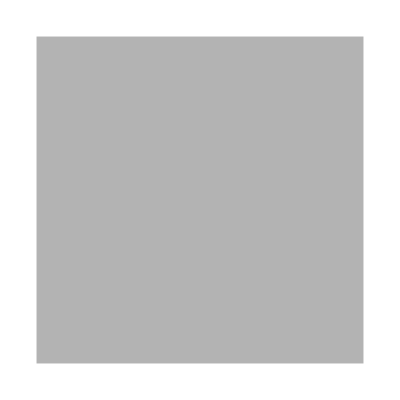
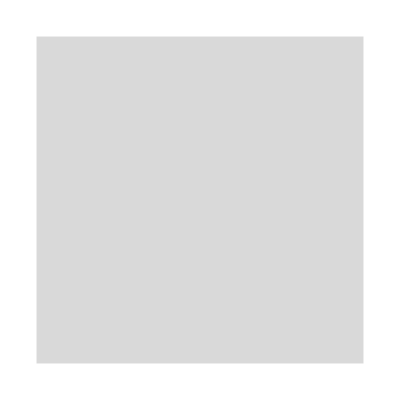

```mathematica
myGray=CMYKColor[0,0,0,.15];
Graphics[{#,Rectangle[]}]&/@{CMYKColor[0,0,0,.3],myGray}
```

```mathematica
d = Import["G:\\Meine Ablage\\Jummeds\\Planungsteam\\Arbeitsgruppen\\Arbeitsmedizin\\Lä.84rmschwerh.94röigkeit MusikerInnen Literatur.81bersicht\\Extract from Full Text Analysis.xlsx"][[1]];

nClassic=Select[d,StringContainsQ[#[[2]],"Classic"]&];
nTrad=Select[d,StringContainsQ[#[[2]],"Traditional"]||StringContainsQ[#[[2]],"Dance"]&];
nRPJ=Select[d,StringContainsQ[#[[2]],"Rock"]||StringContainsQ[#[[2]],"Pop"]||StringContainsQ[#[[2]],"Jazz"]&];
nMil=Select[d,StringContainsQ[#[[2]],"Military"]||StringContainsQ[#[[2]],"Marching"]&];

nNA=Select[d,StringContainsQ[#[[2]],"?"]||StringContainsQ[#[[2]],"Unknown"]||StringContainsQ[#[[2]],"Mixed"]&];
groups={nClassic,nRPJ,nTrad,nMil,nNA};
colorForGroups={"Classical Music"->CMYKColor[0, 0.1, 1., 0.07],"Rock, Pop, Jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"Traditional Music, Dance Music"->CMYKColor[{0, Rational[3, 5], 1, 0}],"Military Music, Marching Band Music"->CMYKColor[{1, Rational[11, 20], 0, 0}],"Unknown, Mixed Genre"->CMYKColor[{0, Rational[9, 10], 1, 0}]};
colorForGroupsLC={"classical music"->CMYKColor[0, 0.1, 1., 0.07],"rock, pop, jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"traditional music, dance music"->CMYKColor[{0, Rational[3, 5], 1, 0}],"military music, marching band music"->CMYKColor[{1, Rational[11, 20], 0, 0}],"unknown, mixed genre"->CMYKColor[{0, Rational[9, 10], 1, 0}]};
colorForGroupsDE={"klassische Musik"->CMYKColor[0, 0.1, 1., 0.07],"Rock, Pop, Jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"unbekanntes, gemischtes Genre"->CMYKColor[{0, Rational[9, 10], 1, 0}],"traditionelle Musik, Tanzmusik"->CMYKColor[{0, Rational[3, 5], 1, 0}],"Militärmusik, Marschmusik"->CMYKColor[{1, Rational[11, 20], 0, 0}]};
```

```mathematica
toGerman={"Classic"->"klassische Musik","Rock, Pop, Jazz"->"Rock, Pop, Jazz","Traditional Music, Dance Music"->"traditionelle Musik, Tanzmusik","Military Music, Marching Band Music"->"Militärmusik, Marschmusik","Classical Music"->"klassische Musik","Traditional"->"traditionelle Musik","Unknown"->"unbekanntes Genre","Mixed"->"gemischte Genre","Dance"->"Tanzmusik","Military Music"->"Militärmusik","Marching Band"->"Marschmusik"}
```

{Classic→klassische Musik,Rock, Pop, Jazz→Rock, Pop, Jazz,Traditional Music, Dance Music→traditionelle Musik, Tanzmusik,Military Music, Marching Band Music→Militärmusik, Marschmusik,Classical Music→klassische Musik,Traditional→traditionelle Musik,Unknown→unbekanntes Genre,Mixed→gemischte Genre,Dance→Tanzmusik,Military Music→Militärmusik,Marching Band→Marschmusik}

## Pie Chart

```mathematica
groupsPiechart=ReverseSort[Association@(#[[2]]->#[[1]]&/@Transpose[{Length/@groups,ToLowerCase/@{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance Music","Military Music, Marching Band Music","Unknown, Mixed Genre"}}])];

chartPieChartGroups=PieChart[groupsPiechart,ChartLabels->Values[groupsPiechart],ImageSize->{600,600},ChartStyle->(Keys[groupsPiechart]/. colorForGroupsLC),LabelStyle->Directive[ FontSize->40,FontFamily->fontStandard],LegendAppearance->{LegendMarkerSize->50,FontFamily->fontStandard},ChartLegends->Keys[groupsPiechart]]
```

-Graphics-

```mathematica
groupsPiechart=ReverseSort[Association@(#[[2]]->#[[1]]&/@Transpose[{Length/@groups,{"klassische Musik","Rock, Pop, Jazz","traditionelle Musik, Tanzmusik","Militärmusik, Marschmusik","unbekanntes, gemischtes Genre"}}])];

chartPieChartGroupsDE=PieChart[groupsPiechart,ChartLabels->Values[groupsPiechart],ImageSize->{600,600},ChartStyle->(Keys[groupsPiechart]/. colorForGroupsDE),LabelStyle->Directive[ FontSize->40,FontFamily->fontStandard],LegendAppearance->{LegendMarkerSize->50,FontFamily->fontStandard},ChartLegends->Keys[groupsPiechart]]
```

-Graphics-

```mathematica
StringSplit[#,", "]&/@Rest[d[[All,2]]];
If[StringContainsQ[#,"?"][[1]]==True,{"Unknown"},#]&/@%;
labelPieChart=ReverseSortBy[Tally@Flatten@%,#[[2]]&]/. {"Classic"->"Classical Music","Dance"->"Dance Music","Traditional"->"Traditional Music","Marching Band"->"Marching Band Music"};

#[[1]]~~ " n="~~ToString[#[[2]]]->#[[2]]&/@%;
Association[%];
chartPieChart=PieChart[%,ChartLabels->Callout[labelPieChart[[All,2]]],ImageSize->{600,600},LabelStyle->Directive[ FontSize->30,FontFamily->fontStandard],ChartStyle->Delete[colors,10],ChartLegends->ToLowerCase/@labelPieChart[[All,1]],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}]
```

-Graphics-

```mathematica
StringSplit[#,", "]&/@Rest[d[[All,2]]];
If[StringContainsQ[#,"?"][[1]]==True,{"Unknown"},#]&/@%;
labelPieChart=ReverseSortBy[Tally@Flatten@%,#[[2]]&];

#[[1]]~~ " n="~~ToString[#[[2]]]->#[[2]]&/@%;
Association[%];
chartPieChartDE=PieChart[%,ChartLabels->Callout[labelPieChart[[All,2]]],ImageSize->{600,600},LabelStyle->Directive[ FontSize->30,FontFamily->fontStandard],ChartStyle->Delete[colors,10],ChartLegends->labelPieChart[[All,1]],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}]/.toGerman
```

-Graphics-

```mathematica
myExportF[{{chartPieChartDE,"Tortendiagramm",600},{chartPieChartGroupsDE,"Tortendiagramm Gruppen",600},{chartPieChart,"Pie Chart",600},{chartPieChartGroups,"Pie Chart Groups",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg}}}

## Histogram n

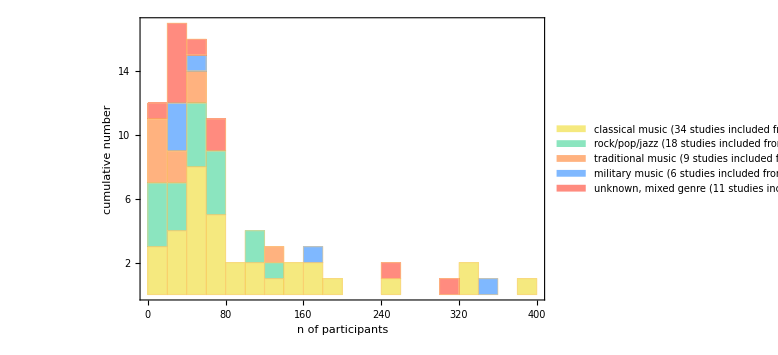

```mathematica
nPart=.
histogNpartGroups[l_List]:=Module[{n,temp},temp=(StringSplit[#,"\n"][[1]]&/@#)&/@l;
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n=Map[{#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&,temp,{2}];
nPart=n;
Histogram[ToExpression/@n[[All,All,1]],
25,
ChartLayout->"Stacked",
ChartLegends->ToLowerCase/@{"Classical Music"~~"\n("~~ToString[Length@n[[1]]] ~~" studies included from "~~ ToString[Length@l[[1]]]~~")", "Rock/Pop/Jazz"~~"\n("~~ToString[Length@n[[2]]] ~~" studies included from "~~ ToString[Length@l[[2]]]~~")","Traditional Music"~~"\n("~~ToString[Length@n[[3]]] ~~" studies included from "~~ ToString[Length@l[[3]]]~~")","Military Music"~~"\n("~~ToString[Length@n[[4]]] ~~" studies included from "~~ ToString[Length@l[[4]]]~~")","Unknown, mixed Genre"~~"\n("~~ToString[Length@n[[5]]] ~~" studies included from "~~ ToString[Length@l[[5]]]~~")"},

ImageSize->Large,
ChartStyle->colors,
myTickStyle[],

Frame->True,
FrameLabel->{"n of participants","cumulative number"},
FrameTicks->{Range[2,18,2],{Range[0,410,40],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18],
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22],

LabelStyle->Directive[ FontSize->20,FontFamily->fontStandard,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]
]



charthistoNGroups=histogNpartGroups[groups[[All,All,4]]]
```

```mathematica
Export[exPath~~"IQR number of participants all data.txt",Quartiles[Flatten[ToExpression/@nPart[[All,All,1]]]]//N]
Quartiles[Flatten[ToExpression/@nPart[[All,All,1]]]]//N

nPartIQ=Sort/@ToExpression/@nPart[[All,All,1]];
maxNList=Length/@nPartIQ;
nPartIQ=SplitBy[#,#>=31|#>=56|#>=111&]&/@nPartIQ;
nPartIQ=Map[Which[Last[#]<=31,31->#,Last[#]<=56,56->#,Last[#]<=111,111->#,Last[#]>=111,112->#,True,{Null}]&,nPartIQ,{2}];
nPartIQ[[All,All,2]]=Map[Length[#]&,nPartIQ[[All,All,2]],{2}];
nPartIQ[[All,All,2]]=nPartIQ[[All,All,2]]/maxNList;
nPartIQ=
{31,56,111,112}/.Join[#,{31->0,56->0,111->0,112->0}]&/@nPartIQ;
nPartIQ=N[nPartIQ*100,3];
nPartIQ=Transpose/@Transpose[{nPartIQ*maxNList/100,nPartIQ}]; (*n and %*)
Total/@nPartIQ;
nPartIQ=Style[TableForm[nPartIQ,TableHeadings->{{"Classical Music n\n%","Rock, Pop, Jazz n\n%","Traditional Music, Dance n\n%","Military Music, Marching Band Music n\n%","Unknown Genre n\n%"},{"1. Quartile","2. Quartile","3. Quartile","4. Quartile"}}],FontFamily->fontStandard,FontSize->fontSize]
Export[exPath~~"Quartiles Study Participants Categories.pdf",nPartIQ]
```

C:\Users\mona_\Desktop\Ausgabe\IQR number of participants all data.txt

{30.,51.5,109.}

| 1. Quartile | 2. Quartile | 3. Quartile | 4. Quartile
Classical Music n
% | 5.
14.7 | 7.
20.6 | 11.
32.4 | 11.
32.4
Rock, Pop, Jazz n
% | 7.
38.9 | 4.
22.2 | 4.
22.2 | 3.
16.7
Traditional Music, Dance n
% | 5.
55.6 | 3.
33.3 | 0
0 | 1.
11.1
Military Music, Marching Band Music n
% | 1.
16.7 | 3.
50. | 0
0 | 2.
33.3
Unknown Genre n
% | 2.
18.2 | 5.
45.5 | 2.
18.2 | 2.
18.2

C:\Users\mona_\Desktop\Ausgabe\Quartiles Study Participants Categories.pdf

```mathematica
nPartIQ=Sort/@ToExpression/@nPart[[All,All,1]];
maxNList=Length/@nPartIQ;
nPartIQ=SplitBy[#,#>=40|#>=80|#>=100|#>=200|#>=300&]&/@nPartIQ;
nPartIQ=Map[Which[Last[#]<=40,40->#,Last[#]<=80,80->#,Last[#]<=100,100->#,Last[#]<=200,200->#,Last[#]<=300,300->#,Last[#]>=300,301->#,True,{Null}]&,nPartIQ,{2}];
nPartIQ[[All,All,2]]=Map[Length[#]&,nPartIQ[[All,All,2]],{2}];
nPartIQ[[All,All,2]]=nPartIQ[[All,All,2]]/maxNList;
nPartIQ=
{40,80,100,200,300,301}/.Join[#,{40->0,80->0,100->0,200->0,300->0,301->0}]&/@nPartIQ;
nPartIQ=N[nPartIQ*100,3];
Total/@nPartIQ;
nPartIQ=Style[TableForm[nPartIQ,TableHeadings->{{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance","Military Music, Marching Band Music","Unknown Genre"},{"<40","<80","<100","<200","<300",">300"}}],FontFamily->fontStandard,FontSize->fontSize]
Export[exPath~~"Distribution Percent Study Participants Categories.pdf",nPartIQ]
```

| <40 | <80 | <100 | <200 | <300 | >300
Classical Music | 20.6 | 38.2 | 5.88 | 23.5 | 2.94 | 8.82
Rock, Pop, Jazz | 38.9 | 44.4 | 0 | 16.7 | 0 | 0
Traditional Music, Dance | 66.7 | 22.2 | 0 | 11.1 | 0 | 0
Military Music, Marching Band Music | 50. | 16.7 | 0 | 16.7 | 0 | 16.7
Unknown Genre | 54.5 | 27.3 | 0 | 0 | 9.09 | 9.09

C:\Users\mona_\Desktop\Ausgabe\Distribution Percent Study Participants Categories.pdf

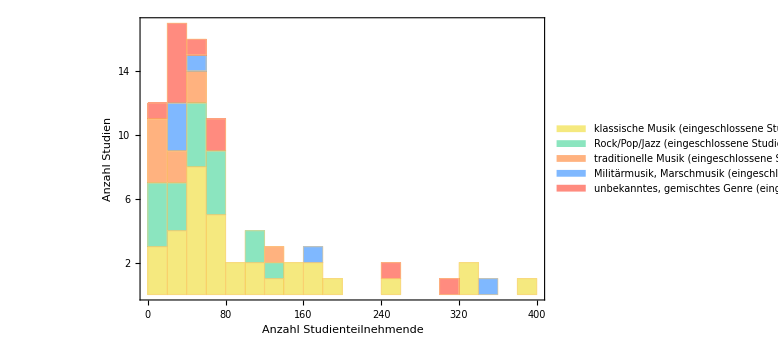

```mathematica
histogNpartGroupsDE[l_List]:=Module[{n,temp},temp=(StringSplit[#,"\n"][[1]]&/@#)&/@l;
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n=Map[{#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&,temp,{2}];
Histogram[ToExpression/@n[[All,All,1]],25,FrameTicks->{Range[2,18,2],{Range[0,410,40],Automatic}},ImageSize->Large,ChartLegends->{"klassische Musik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[1]]] " von "<> ToString[Length@l[[1]]]<>")", "Rock/Pop/Jazz"<>"\n (eingeschlossene Studien: " <>ToString[Length@n[[2]]] " von "<> ToString[Length@l[[2]]]<>")","traditionelle Musik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[3]]]" von "<> ToString[Length@l[[3]]]<>")","Militärmusik, Marschmusik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[4]]]" von "<> ToString[Length@l[[4]]]<>")","unbekanntes, gemischtes Genre"<>"\n(eingeschlossene Studien: "~~ToString[Length@n[[5]]] ~~" von "~~ ToString[Length@l[[5]]]~~")"},LabelStyle->Directive[ FontSize->20,FontFamily->fontStandard,Black],ChartLayout->"Stacked",myTickStyle[],ChartStyle->colors,Frame->True,FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18],FrameLabel->{"Anzahl Studienteilnehmende","Anzahl Studien"},FrameStyle->Directive[FontFamily->fontStandard,FontSize->22],LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}]
]

charthistoNGroupsDE=histogNpartGroupsDE[groups[[All,All,4]]]
```

```mathematica
myExportF[{{charthistoNGroupsDE,"Histogramm Anzahl Studienteilnehmende",600},{charthistoNGroups,"Histogram n Participants",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg}}}

## Gender analysis

```mathematica
63/2//N
```

31.5

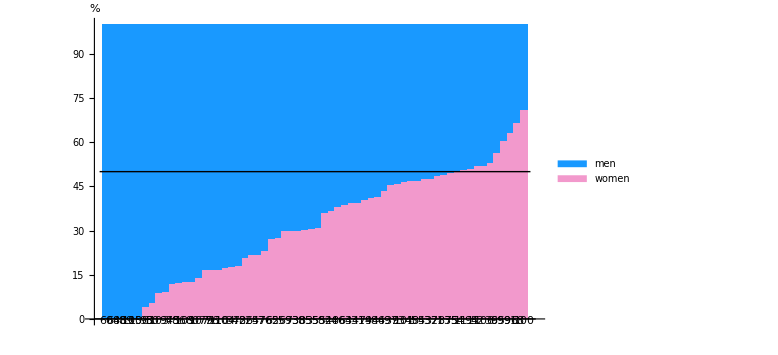
-Graphics-(64 studies included from 79)
sex distribution as bar chart

```mathematica
datagenderAnalysis=.
genderAnalysis=.
genderAnalysis[l_List]:=Module[{n,temp,ngender,genderfrac,ngenderTitles,genderfracTitles,chartTitleNumbers},temp=Map[{StringSplit[#[[1]],"\n"][[1]],#[[2]]}&,l,{1}];
temp=If[#[[1]]=!="-",{StringSplit[#[[1]]," "],#[[2]]},Nothing]&/@temp;
n={{#[[1,1]],If[#[[1,2]]!="(?)",{StringCases[#[[1,2]],"("~~a__~~"f"->a],StringCases[#[[1,2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]},#[[2]]}&/@temp;ngenderTitles={ToExpression/@Flatten[#[[1]]],#[[2]]}&/@Select[n,#[[1,2,1,1]]!="?"&];
ngender=ngenderTitles[[All,1]];
genderfracTitles={{#[[1,2]]/(#[[1,2]]+#[[1,3]]),#[[1,3]]/(#[[1,2]]+#[[1,3]])}*100,#[[2]]}&/@ngenderTitles ;(*female, male portion*)
genderfracTitles=SortBy[genderfracTitles,#[[1,1]]&];
genderfrac=genderfracTitles[[All,1]];

chartTitleNumbers=(titleReplaceF[#]&/@genderfracTitles[[All,2]]);
chartTitleNumbers=chartTitleNumbers /. replaceTitle

;
chartTitleNumbers=Flatten[{"\n"~~#[[1]],"\n\n"~~#[[2]],"\n\n\n"~~#[[3]]}&/@Partition[chartTitleNumbers,3,3,1,""]];

datagenderAnalysis=genderfrac;


Labeled[
Show[
BarChart[genderfrac,
BarSpacing->0,
ChartLayout->"Stacked",
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"women","men"},
ImagePadding->{{Automatic,Automatic}, {90,Automatic}},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},
ChartLabels->{myStyle[#,11]&/@chartTitleNumbers,None},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],
LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}]

,Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Column[{myStyle["("~~ToString[Length@ngender]~~" studies included from "~~ToString[Length@l]~~")",16],Style["sex distribution as bar chart",FontSize->20,FontFamily->fontStandard]},Alignment->Center,Spacings->{Automatic, 1}]
]
]

chartHistoGenderEN=genderAnalysis[Rest@d[[All,{4,1}]]]
```

```mathematica
myExportF[{{chartHistoGenderEN,"Barchart Sex Portion",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg}}}

```mathematica
Export[exPath~~"sex portion IQR.pdf",mySubJoin[Round/@N[Quartiles[#]]&/@Transpose@datagenderAnalysis,{"women portion IQR"->1,"men portion IQR"->2}]]
```

C:\Users\mona_\Desktop\Ausgabe\sex portion IQR.pdf

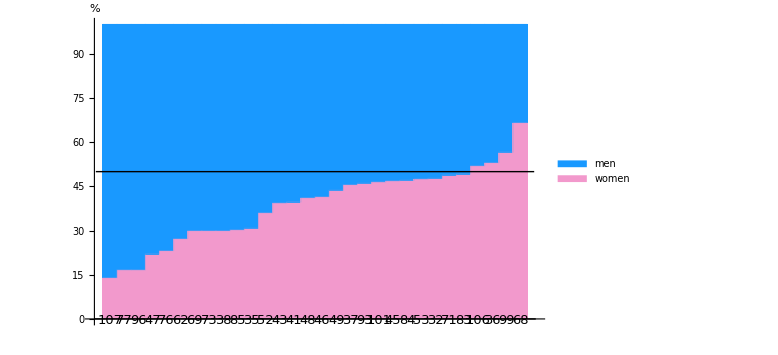
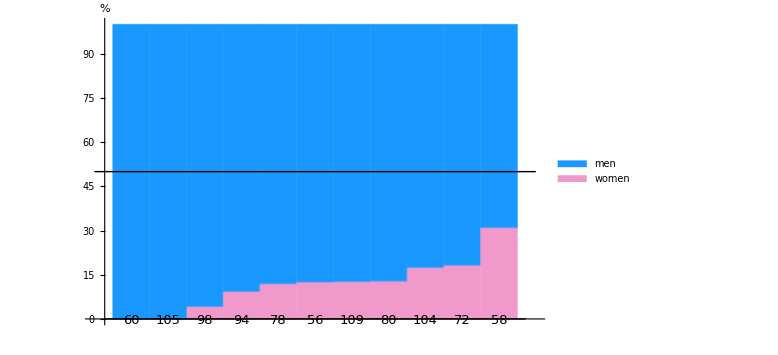
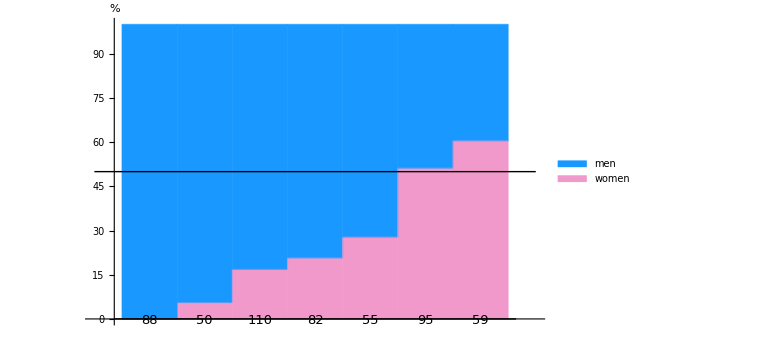
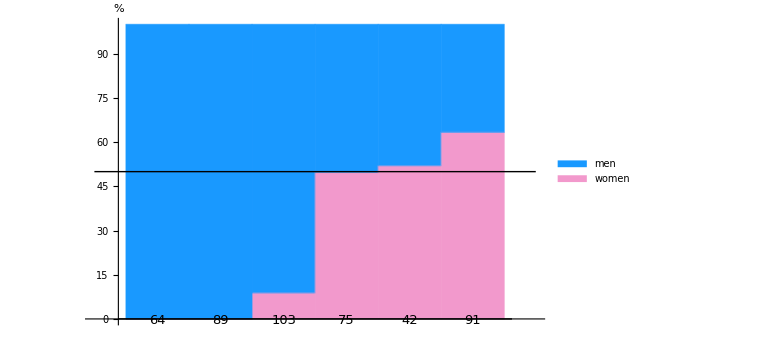
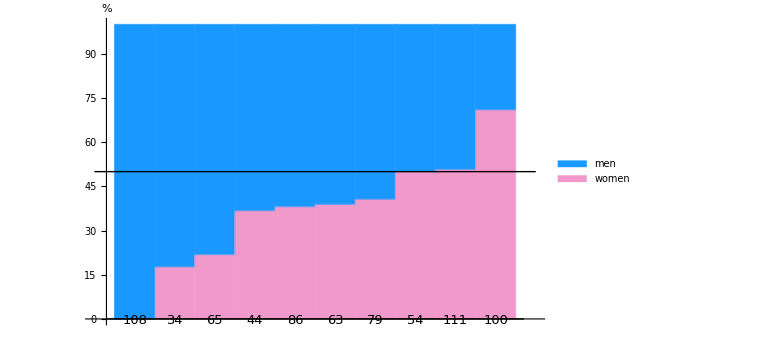
{-Graphics-sex distribution as bar chart
(30 studies included from 34)classical music,-Graphics-sex distribution as bar chart
(11 studies included from 18)rock/pop/jazz,-Graphics-sex distribution as bar chart
(7 studies included from 9)traditional music,-Graphics-sex distribution as bar chart
(6 studies included from 6)military music,-Graphics-sex distribution as bar chart
(10 studies included from 11)unknown, mixed genre}

```mathematica
genderAnalysis=.
genderAnalysis[l_List]:=Module[{n,temp,ngender,genderfrac,ngenderTitles,genderfracTitles,chartTitleNumbers},temp=Map[{StringSplit[#[[1]],"\n"][[1]],#[[2]]}&,l,{1}];
temp=If[#[[1]]=!="-",{StringSplit[#[[1]]," "],#[[2]]},Nothing]&/@temp;
n={{#[[1,1]],If[#[[1,2]]!="(?)",{StringCases[#[[1,2]],"("~~a__~~"f"->a],StringCases[#[[1,2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]},#[[2]]}&/@temp;ngenderTitles={ToExpression/@Flatten[#[[1]]],#[[2]]}&/@Select[n,#[[1,2,1,1]]!="?"&];
ngender=ngenderTitles[[All,1]];
genderfracTitles={{#[[1,2]]/(#[[1,2]]+#[[1,3]]),#[[1,3]]/(#[[1,2]]+#[[1,3]])}*100,#[[2]]}&/@ngenderTitles ;(*female, male portion*)
genderfracTitles=SortBy[genderfracTitles,#[[1,1]]&];
genderfrac=genderfracTitles[[All,1]];

chartTitleNumbers=(titleReplaceF[#]&/@genderfracTitles[[All,2]]);
chartTitleNumbers=chartTitleNumbers /. replaceTitle;
chartTitleNumbers=Flatten[{"\n"~~#[[1]],"\n\n"~~#[[2]],"\n\n\n"~~#[[3]]}&/@Partition[chartTitleNumbers,3,3,1,""]];

datagenderAnalysis=genderfrac;


Labeled[
Show[
BarChart[genderfrac,
BarSpacing->0,
ChartLayout->"Stacked",
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"women","men"},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},
ChartLabels->{myStyle[#,13]&/@chartTitleNumbers,None},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}],

Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Style["sex distribution as bar chart\n("~~ToString[Length@ngender] ~~" studies included from "~~ ToString[Length@n]~~")",FontSize->18,FontFamily->fontStandard],Spacings->{1.3, 1.3}]


(*}*)
]

genderAnalysis[#]&/@groups[[All,All,{4,1}]];
chartHistoGenderGroupsEN=Labeled[#[[1]],#[[2]], Top]&/@Transpose[{%,Style[#,FontFamily->fontStandard,FontSize->22,Bold]&/@ToLowerCase/@{"Classical Music","Rock/Pop/Jazz","Traditional Music","Military Music","Unknown, Mixed Genre"}}]
```

```mathematica
myExportF[Transpose[{chartHistoGenderGroupsEN,{"Barchart Sex Portion Classic","Barchart Sex Portion Rock Pop Jazz","Barchart Sex Portion Traditional","Barchart Sex Portion Military Music","Barchart Sex Portion Unknown Genre"},{150,150,150,150,150}}]]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg}}}

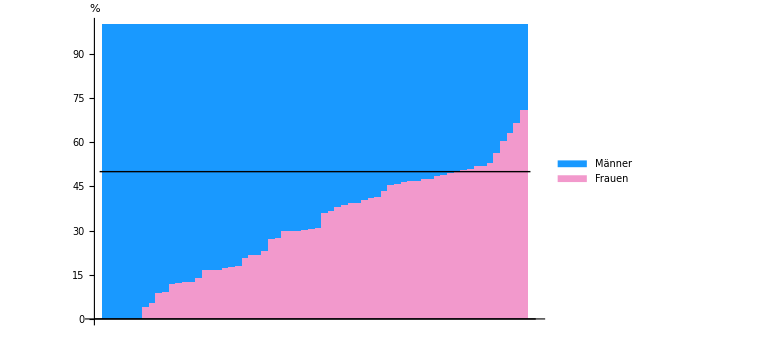
-Graphics-Geschlechterverteilung als Balkendiagramm
(64 Studien von 79 eingeschlossen)

{{{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg},{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg},{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg}}}

{9,36.2995,0.0000350768}

C:\Users\mona_\Desktop\Ausgabe\Pearson Chi2Test.txt

```mathematica
genderfrac=.
genderAnalysisDE[l_List]:=Module[{n,temp,ngender},temp=StringSplit[#,"\n"][[1]]&/@Rest[l];
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n={#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&/@temp;ngender=ToExpression/@Flatten[#]&/@Select[n,#[[2,1,1]]!="?"&];
genderfrac={#[[2]]/(#[[2]]+#[[3]]),#[[3]]/(#[[2]]+#[[3]])}*100&/@ngender;

(*{Show[ListPlot[genderfrac,AxesLabel->myStyleFunction[{"fraction women","fraction men"}],myTickStyle,PlotStyle->mycolor],Plot[.5,{x,0,0.7},PlotStyle->mycolor]],
Labeled[Histogram[genderfrac[[All,1]]*100,10,ChartStyle->mycolor],myStyle["Histogram of fraction female \n("~~ToString[Length@n] ~~" studies included from "~~ ToString[Length@l]~~")"]],FindDistribution[genderfrac[[All,1]]],*)

Labeled[
Show[
BarChart[SortBy[genderfrac,First],
BarSpacing->0,
ChartLayout->"Stacked",
Background->White,
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"Frauen","Männer"},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}

],

Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Style["Geschlechterverteilung als Balkendiagramm\n("~~ToString[Length@ngender] ~~" Studien von "~~ ToString[Length@Rest@l]~~" eingeschlossen)",FontSize->18,FontFamily->fontStandard]]

(*}*)
]


chartHistoGenderDE=genderAnalysisDE[d[[All,4]]]

myExportF[{{chartHistoGenderDE,"Geschlechtsverteilung alle Studien",600}}]




Needs["HypothesisTesting`"]
statTest=PearsonChiSquareTest[genderfrac[[All,1]],genderfrac[[All,2]],{"DegreesOfFreedom","TestStatistic","PValue"}]
(*Chi-Quadrat(4)=70.788,p<.001*)
Export[exPath~~"Pearson Chi2Test.txt",statTest]
```

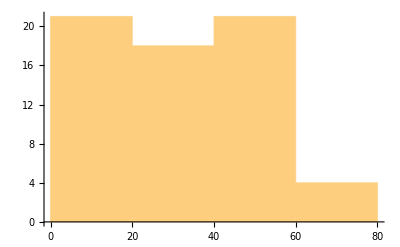
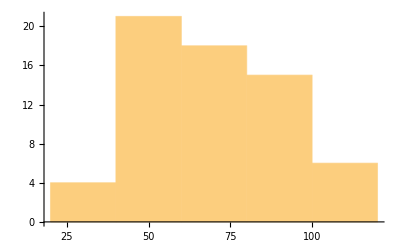

{UniformDistribution[{-0.0984364,70.9431}],MixtureDistribution[{0.648921,0.245194,0.105885},{NormalDistribution[56.6821,12.909],NormalDistribution[85.6028,5.40885],NormalDistribution[100.004,0.0665763]}]}

```mathematica
Histogram/@Transpose@genderfrac
FindDistribution/@Transpose@genderfrac
```

## Age Analysis

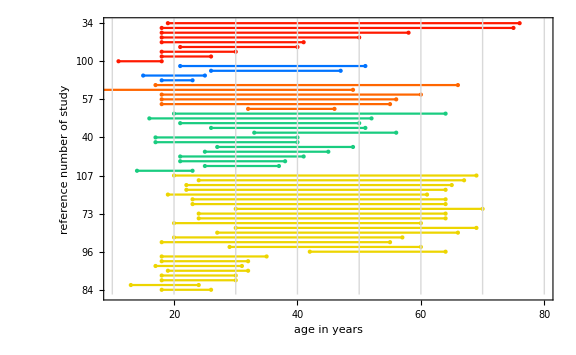
-Graphics-

-Graphics- classical music
         (25 studies included from 35)-Graphics- rock/pop/jazz
         (13 studies included from 18)-Graphics- traditional music
         (6 studies included from 9)-Graphics- military music
         (4 studies included from 6)-Graphics- unknown, mixed genre
         (9 studies included from 11)

```mathematica
ageAnalysisGroups=.
ageAnalysisGroups[l_List]:=Module[{agerange,agerangesorted,agerangeTitles,intervallist,plotstyleSet,frametickNumbers,frametickTitle},
agerange={(StringSplit[#[[1]],"\n"]),#[[2]]}&/@#&/@l;
agerange=Map[Select[#,#[[1]]=!="-"&]&,Transpose/@myT[agerange[[All,All,1,1]],agerange[[All,All,2]]],{1}];
agerange= Map[{ToExpression/@(StringSplit[#[[1]],{"-","–"}]),#[[2]]}&,agerange,{2}];
agerange= Map[{#[[1,2]]-#[[1,1]],#[[1,1]],#[[1,2]],#[[2]]}&,agerange,{2}];
agerangesorted=Map[SortBy[#,First]&,agerange,{1}];
agerangeTitles=(titleReplaceF/@Flatten[agerangesorted[[All,All,-1]]])/. replaceTitle;


intervallist=Map[Interval[{#[[2]],#[[3]]}]&,agerangesorted,{2}];
frametickNumbers={Range[1,Length@Flatten@intervallist,2],Range[2,Length@Flatten@intervallist,2]};

agerangeTitles=agerangeTitles[[#]]&/@Flatten@frametickNumbers;

frametickTitle=Transpose/@Transpose[{frametickNumbers,{agerangeTitles[[1;;Length@frametickNumbers[[1]]]],agerangeTitles[[Length@frametickNumbers[[1]]+1;;-1]]}}];


plotstyleSet=Table[#[[1]],Length@#[[2]]]&/@Transpose[{colors[[1;;Length@intervallist]],intervallist}];


Labeled[

Show[


NumberLinePlot[
Flatten@intervallist,{x,10,80},
TicksStyle->Directive[FontFamily->fontStandard,fontSize],
ImageSize->Large,
PlotStyle->Flatten@plotstyleSet,

Frame->True,
FrameTicks->{frametickTitle,
{Range[0,90,10],Automatic}},
FrameTicksStyle->{Directive[FontFamily->fontStandard,FontSize->12,Black],Directive[FontFamily->fontStandard,FontSize->18,Black]},
FrameLabel->(Style[#,FontFamily->fontStandard,FontSize->18,Black]&/@{"age in years","reference number of study"})
],

Graphics[{ColorConvert[LightGray,"CMYK"],#}]&/@(Map[Line[{{#[[1]],0},{#[[1]],#[[2]]}}]&,Transpose@{Range[10,80,10],Table[Length[Flatten@intervallist]+1,Length@Range[10,80,10]]}])(*,
Graphics[{Thick,#}]&/@{Line[{{2,0},{2,40}}],Line[{{2,40},{95,40}}],Line[{{85,40},{85,0}}]}*)
]
,

Row[Row/@Transpose[{Table[Graphics[{i,Rectangle[]},ImageSize->30],{i,colors[[1;;5]]}],Style[#,FontFamily->fontStandard,FontSize->18]&/@ToLowerCase/@{" Classical Music\n         ("~~ToString[Length@intervallist[[1]]] ~~" studies included from "~~ ToString[Length@l[[1]]]~~")"," Rock/Pop/Jazz\n         ("~~ToString[Length@intervallist[[2]]] ~~" studies included from "~~ ToString[Length@l[[2]]]~~")"," Traditional Music\n         ("~~ToString[Length@intervallist[[3]]] ~~" studies included from "~~ ToString[Length@l[[3]]]~~")"," Military Music\n         ("~~ToString[Length@intervallist[[4]]] ~~" studies included from "~~ ToString[Length@l[[4]]]~~")"," Unknown, Mixed Genre\n         ("~~ToString[Length@intervallist[[5]]] ~~" studies included from "~~ ToString[Length@l[[5]]]~~")"}}],"\n"],Right,Spacings->{2,2}]

]


chartAge=ageAnalysisGroups[Map[Transpose,Transpose[{groups[[All,All,5]],groups[[All,All,1]]}],{1}]]
```

```mathematica
myExportF[{{chartAge,"Distribution of Age Ranges",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg},{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg},{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg}}}

```mathematica
ageAnalysisGroupsDE[l_List]:=Module[{agerange,agerangesorted,intervallist,plotstyleSet,chart},agerange=(StringSplit[#,"\n"]&/@#)&/@l;
agerange=StringSplit[#,{"-","–"}]&/@(Select[First/@#,#!="-"&&#!="?"&]&/@agerange);
agerange=Map[ToExpression,agerange,{2}];
agerange=Map[{#[[2]]-#[[1]],#[[1]],#[[2]]}&,agerange/.Null->10,{2}];
agerangesorted=SortBy[#,First][[All,2;;3]]&/@agerange;
intervallist=Map[Interval[{#[[1]],#[[2]]}]&,agerangesorted,{2}];
plotstyleSet=Table[#[[1]],Length@#[[2]]]&/@Transpose[{colors[[1;;Length@intervallist]],intervallist}];


chart=Labeled[

Show[


NumberLinePlot[
Flatten@intervallist,{x,10,80},
ImageSize->Large,
PlotStyle->Flatten@plotstyleSet,

Frame->True,
FrameTicks->{{Automatic,Automatic},
{Range[0,90,10],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->(Style[#,FontFamily->fontStandard,FontSize->18,Black]&/@{"Alter in Jahren","Anzahl"})
],

Graphics[{ColorConvert[LightGray,"CMYK"],#}]&/@(Map[Line[{{#[[1]],0},{#[[1]],#[[2]]}}]&,Transpose@{Range[10,80,10],Table[Length[Flatten@intervallist]+1,Length@Range[10,80,10]]}])(*,
Graphics[{Thick,#}]&/@{Line[{{2,0},{2,40}}],Line[{{2,40},{95,40}}],Line[{{85,40},{85,0}}]}*)
]
,

Row[Row/@Transpose[{Table[Graphics[{i,Rectangle[]},ImageSize->30],{i,colors[[1;;5]]}],Style[#,FontFamily->fontStandard,FontSize->18]&/@{" klassische Musik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[1]]] ~~" von "~~ ToString[Length@l[[1]]]~~")"," Rock/Pop/Jazz\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[2]]] ~~" von "~~ ToString[Length@l[[2]]]~~")"," traditionelle Musik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[3]]] ~~" von "~~ ToString[Length@l[[3]]]~~")"," Militärmusik und Marschmusik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[4]]] ~~" von "~~ ToString[Length@l[[4]]]~~")"," unbekanntes Genre\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[5]]] ~~" von "~~ ToString[Length@l[[5]]]~~")"}}],"\n"],Right,Spacings->{1, 2}];

Rasterize[chart,ImageResolution->600]
]


chartAgeDE=ageAnalysisGroupsDE[groups[[All,All,5]]]
```

-Graphics-

```mathematica
myExportF[{{chartAgeDE,"Verteilung der Altersspannen",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg},{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg},{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg}}}

## Years of Practice

{5.,5.,1.,5.,5.,0.4,5.,5.,5.,1.,1.,5.,10.,5.,11.,6.,5.,16.,10,0.5,8.,2.,8.,1.,10.,5.,3.,5.,1.,10.,3.,7.,2.,2.,1.,0.,5.,8.}

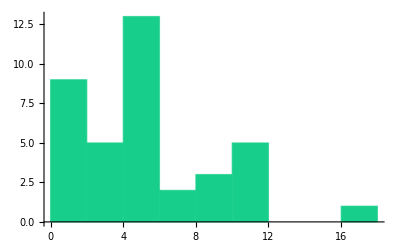
-Graphics-Histogram of years of practice
(38 studies included from 80)

```mathematica
yOfPractice=ToExpression/@Select[StringSplit[#,"\n"][[1]]&/@Rest[ToString/@d[[All,6]]],DigitQ[Characters[#][[1]]]&]
Labeled[Histogram[yOfPractice,10,myTickStyle,ChartStyle->mycolor,Ticks->{Range[0,17,2],Automatic}],myStyle["Histogram of years of practice\n("~~ToString[Length@yOfPractice] ~~" studies included from "~~ ToString[Length@d]~~")"]]
```

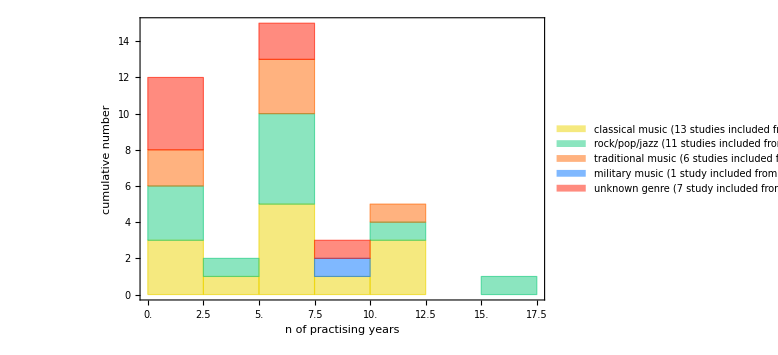

```mathematica
yOfPractice=Map[ToString,groups[[All,All,6]],{2}];
yOfPractice=Map[StringSplit[#,"\n"][[1]]&,yOfPractice,{2}];
yOfPractice=Map[Select[#,DigitQ[Characters[#][[1]]]&]&,yOfPractice];
yOfPractice=Map[ToExpression,yOfPractice,{2}];

chartPracticeY=
Histogram[
yOfPractice,{2.5},myTickStyle,ChartLayout->"Stacked",ImageSize->Large,

Frame->True,FrameTicks->{{Automatic,All},
{Table[i,{i,0,18, 2.5}],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->{"n of practising years","cumulative number"},
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22,Black],

ChartStyle->colors,
ChartLegends->ToLowerCase/@{"Classical Music"~~"\n("~~ToString[Length@yOfPractice[[1]]] ~~" studies included from "~~ ToString[Length@groups[[1]]]~~")", "Rock/Pop/Jazz"~~"\n("~~ToString[Length@yOfPractice[[2]]] ~~" studies included from "~~ ToString[Length@groups[[2]]]~~")","Traditional Music"~~"\n("~~ToString[Length@yOfPractice[[3]]] ~~" studies included from "~~ ToString[Length@groups[[3]]]~~")","Military Music"~~"\n("~~ToString[Length@yOfPractice[[4]]] ~~" study included from "~~ ToString[Length@groups[[4]]]~~")","Unknown Genre"~~"\n("~~ToString[Length@yOfPractice[[5]]] ~~" study included from "~~ ToString[Length@groups[[5]]]~~")"},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20 ,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]
```

```mathematica
myExportF[{{chartPracticeY,"Histogram of minimal years as practising musician",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg}}}

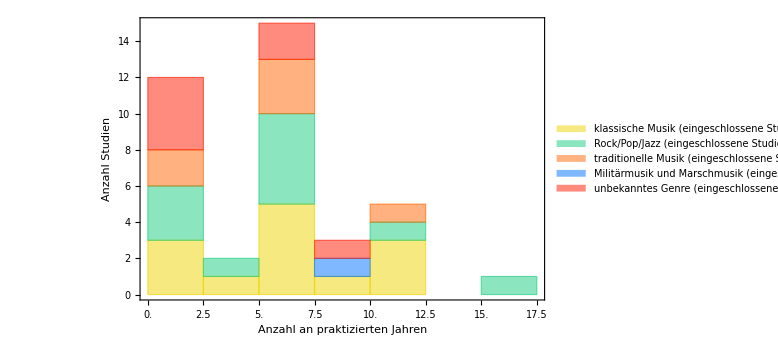

```mathematica
yOfPractice=Map[ToString,groups[[All,All,6]],{2}];
yOfPractice=Map[StringSplit[#,"\n"][[1]]&,yOfPractice,{2}];
yOfPractice=Map[Select[#,DigitQ[Characters[#][[1]]]&]&,yOfPractice];
yOfPractice=Map[ToExpression,yOfPractice,{2}];

chartPracticeYDE=
Histogram[
yOfPractice,{2.5},myTickStyle[],ChartLayout->"Stacked",ImageSize->Large,

Frame->True,FrameTicks->{{Automatic,All},
{Table[i,{i,0,18, 2.5}],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->{"Anzahl an praktizierten Jahren","Anzahl Studien"},
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22,Black],

ChartStyle->colors,
ChartLegends->{"klassische Musik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[1]]] ~~" von "~~ ToString[Length@groups[[1]]]~~")", "Rock/Pop/Jazz"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[2]]] ~~" von "~~ ToString[Length@groups[[2]]]~~")","traditionelle Musik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[3]]] ~~" von "~~ ToString[Length@groups[[3]]]~~")","Militärmusik und Marschmusik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[4]]] ~~" von "~~ ToString[Length@groups[[4]]]~~")","unbekanntes Genre"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[5]]] ~~" von "~~ ToString[Length@groups[[5]]]~~")"},
LabelStyle->Directive[FontFamily->fontStandard,FontSize->20 ,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]
```

```mathematica
myExportF[{{chartPracticeYDE,"Histogramm für minimale Spieljahresanzahl",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg}}}

```mathematica
(*poor data*)
com=Rest[d[[All,11]]];
npd=Length@com
nPoorpd=Length[Select[com,StringContainsQ[ToString@#,"poor"]&]]
nPoorPerc=nPoorpd/npd//N
Export[exPath~~"Poor Data.txt","all "~~ToString@npd~~"\npoor "~~ToString@nPoorpd~~"\npercent "~~ToString@nPoorPerc]
```

79

32

0.405063

C:\Users\mona_\Desktop\Ausgabe\Poor Data.txt

```mathematica
audiometryFrList= ToExpression/@ StringSplit["125,250,500,1000,2000,3000,4000,6000,8000,9000,10000,11200,12500,14000,16000",","];
nameresult[l_List]:=Module[{p},p=l[[1]]; Append[#,p]&/@l[[2]]];
nameresultList[l_List]:=Module[{p},p=l[[{1,3}]]; Append[#,p]&/@l[[2]]];
pos[v_]:=Module[{},Position[audiometryFrList,v]];
greenColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0.01+i*0.7/m,0,0.01+i 0.6/m,0}]]
redColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0,0.01+i*0.9/m,0.01+i 1/m,0}]]
yellowColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0.01+i*0.1/m,0.01+i 0.1/m,0.01+i .9/m,0}]]
```

```mathematica
links=Import["C:\\Users\\mona_\\OneDrive\\Jummeds\\Arbeitsgruppen\\Arbeitsmedizin\\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\\Literaturliste mit Titel, Autoren, DOI.xlsx"][[1]];
linksReplace=(Rest@links[[All,{1,4,2,8}]])/.{"","","",""}->Nothing;

newRefNumber=Import["C:\\Users\\mona_\\OneDrive\\Jummeds\\Arbeitsgruppen\\Arbeitsmedizin\\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\\Programmierung\\Literature Publication Number Vancouver.txt"];
newRefNumber=StringSplit[newRefNumber,"\n"];

titleReplaceF=.
titleReplaceF[t_String]:=StringReplace[ToLowerCase[t]," "->""]

replaceLink=titleReplaceF[#[[1]]]->"["<>#[[1]]<>"    "<>#[[3]]<>" ("<>If[StringLength[ToString[#[[4]]]]>4,StringJoin[Characters[ToString[#[[4]]]][[1;;4]]],""]<>")]("<>#[[2]]<>")"&/@linksReplace; (*für online Veröffentlichung s. Repository*)


replaceTitleforWeb=titleReplaceF[#[[1]]]->#[[1]]<>"    "<>#[[3]]<>" ("<>If[StringLength[ToString[#[[4]]]]>4,StringJoin[Characters[ToString[#[[4]]]][[1;;4]]],""]<>")"&/@linksReplace; 
(*
vormals mit ausgeschriebenem Titel
*)

replaceTitle=Flatten[Function[title,If[StringContainsQ[titleReplaceF@#,titleReplaceF[title[[1]]]],titleReplaceF[title[[1]]]->StringCases[#,DigitCharacter..][[1]],Nothing]&/@newRefNumber][#]&/@linksReplace];
(*für Abbildungen, hier wird die Vancouver-Zitatnummer ausgelesen*)
```

Import::nffil: File C:\Users\mona_\OneDrive\Jummeds\Arbeitsgruppen\Arbeitsmedizin\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\Literaturliste mit Titel, Autoren, DOI.xlsx not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧⟦All,{1,4,2,8}⟧ is longer than depth of object.

Part::partd: Part specification All⟦{1,4,2,8}⟧ is longer than depth of object.

Import::nffil: File C:\Users\mona_\OneDrive\Jummeds\Arbeitsgruppen\Arbeitsmedizin\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\Programmierung\Literature Publication Number Vancouver.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,
].

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in [<>All⟦1⟧<>    <>All⟦3⟧<> (All[)](<>All⟦2⟧<>).

StringJoin::string: String expected at position 4 in [<>All⟦1⟧<>    <>All⟦3⟧<> (All[)](<>All⟦2⟧<>).

StringJoin::string: String expected at position 6 in [<>All⟦1⟧<>    <>All⟦3⟧<> (All[)](<>All⟦2⟧<>).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Part::pkspec1: The expression titleReplaceF[1]→[<>1<>    <>2<> ()](<>4<>) cannot be used as a part specification.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in All⟦1⟧<>    <>All⟦3⟧<> (All[).

StringJoin::string: String expected at position 3 in All⟦1⟧<>    <>All⟦3⟧<> (All[).

StringJoin::string: String expected at position 1 in 1<>    <>2<> ().

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Part::pkspec1: The expression titleReplaceF[1]→1<>    <>2<> () cannot be used as a part specification.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[titleReplaceF[$Failed],titleReplaceF[All⟦1⟧]].

StringExpression::invld: Element titleReplaceF[All⟦1⟧] is not a valid string or pattern element in titleReplaceF[All⟦1⟧].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[If[StringContainsQ[titleReplaceF[$Failed],titleReplaceF[All⟦1⟧]],titleReplaceF[All⟦1⟧]→StringCases[$Failed,DigitCharacter..]⟦1⟧,Nothing],If[StringContainsQ[
,titleReplaceF[All⟦1⟧]],titleReplaceF[All⟦1⟧]→StringCases[
,DigitCharacter..]⟦1⟧,Nothing]].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[titleReplaceF[$Failed],titleReplaceF[1]].

StringExpression::invld: Element titleReplaceF[1] is not a valid string or pattern element in titleReplaceF[1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[If[StringContainsQ[titleReplaceF[$Failed],titleReplaceF[1]],titleReplaceF[{1,4,2,8}⟦1⟧]→StringCases[$Failed,DigitCharacter..]⟦1⟧,Nothing],If[StringContainsQ[
,titleReplaceF[1]],titleReplaceF[{1,4,2,8}⟦1⟧]→StringCases[
,DigitCharacter..]⟦1⟧,Nothing]].

Part::pkspec1: The expression StringSplit[If[StringContainsQ[titleReplaceF[$Failed],titleReplaceF[1]],titleReplaceF[{1,4,2,8}⟦1⟧]→StringCases[$Failed,DigitCharacter..]⟦1⟧,Nothing],If[StringContainsQ[
,titleReplaceF[1]],titleReplaceF[{1,4,2,8}⟦1⟧]→StringCases[
,DigitCharacter..]⟦1⟧,Nothing]] cannot be used as a part specification.

```mathematica
graphRectangle[l_List]:=Module[{ex,r},ex=ToExpression/@Flatten[l][[1;;2]];r=ex[[1]]/ex[[2]];Graphics[{l[[3]],Rectangle[{0,0},{r,.15}],"Grün",Rectangle[{r,0},{1,.15}]}]/.colorlist]
graphRectangle[{{3},{16},"Zitronengelb"}]
```

-Graphics-

```mathematica
groups[[All,All,{1,10,4}]]
```

## Result Analysis

```mathematica
Length@Flatten[groups[[All,All,{1,-1}]],1]
```

79

```mathematica
Length@Rest@d[[All,{1,-1}]]
```

79

ToExpression::sntxi: Incomplete expression; more input is needed .

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

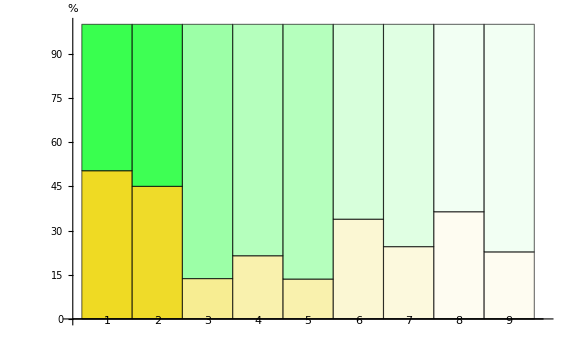
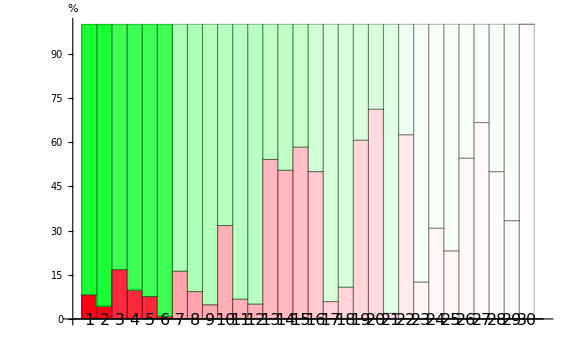
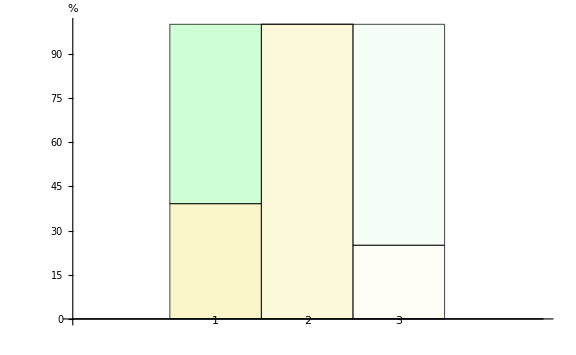
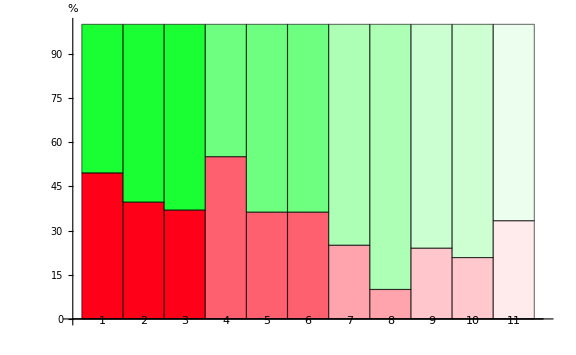
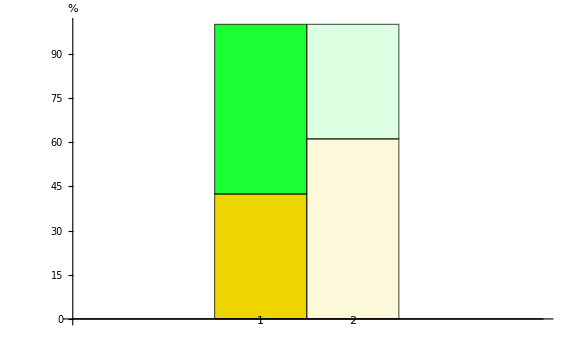
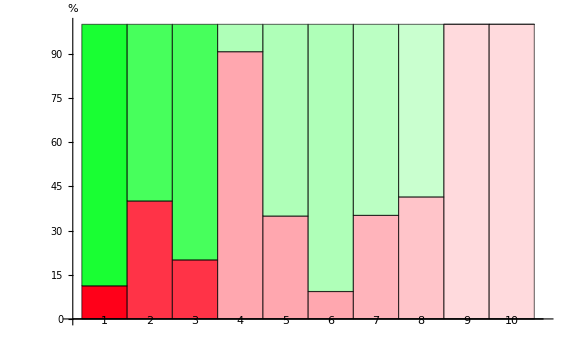
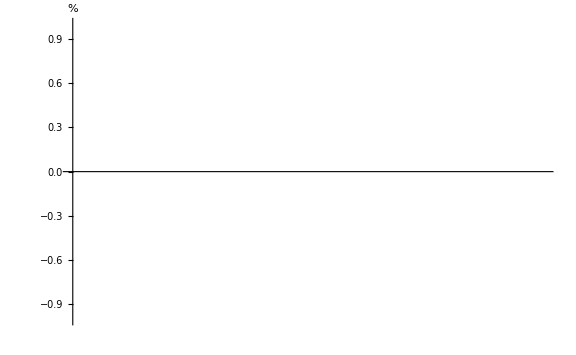
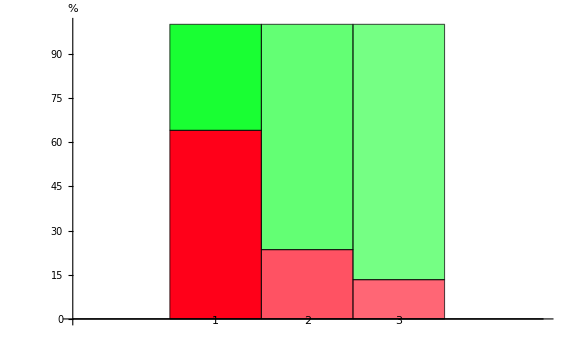
{-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | music students | 170 | 338 | notch | - | 6000 | n/a | 70
2 | music students (classical music, 19 jazz) | 148 | 329 | notch >15 dB | r/l | 4000-6000 | n/a | 101
3 | music students | 23 | 168 | notch >15 dB | - | 4000-6000 | n/a | 71
4 | symphony orchestra musicians | 27 | 126 | notches | l | 4000-6000 | n/a | 93
5 | symphony orchestra musicians | 17 | 126 | notches | r | 4000-6000 | n/a | 93
6 | orchestra musicians [ears reported for affected persons and sample size] | 23 | 68 | notches | - | - | n/a | 92
7 | orchestra musicians | 13 | 53 | notch 15 dB | r+l | 3000-6000 | yes | 46
8 | adolescent musicians | 8 | 22 | notches | l | 3000-6000 | n/a | 62
9 | adolescent musicians | 5 | 22 | notches | r | 4000-6000 | n/a | 62-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | flute players | 17 | 392 | loss 20 dB | r+l | 4000-8000 | n/a | 107
2 | double bass players | 32 | 392 | loss | l | 4000-8000 | n/a | 107
3 | music students (classical music, 19 jazz) | 55 | 329 | loss | l | 6000 | n/a | 101
4 | music students (classical music, 19 jazz) | 32 | 329 | loss | r | 6000 | n/a | 101
5 | music students (classical music, 19 jazz) | 25 | 329 | loss | r+l | 6000 | n/a | 101
6 | music students (classical music, 19 jazz) | 3 | 329 | loss | r+l | 4000 | n/a | 101
7 | french horn players | 23 | 142 | loss | - | - | yes | 49
8 | 7 musicians playing small strings, 3 woodwind players, 2 brasswind players and 1 percussionist | 13 | 140 | loss | - | 3000-8000 | yes | 38
9 | symphony orchestra musicians (88.9% are older musicians that have the loss) | 6 | 126 | loss >25 dB | - | - | n/a | 93
10 | musicians in 6 year follow-up who are 50-59 years | 39 | 123 | loss | - | 4000-6000 | n/a | 107
11 | orchestra musicians | 8 | 119 | loss >15 dB | l | 6000 | n/a | 83
12 | orchestra musicians | 6 | 119 | loss >15 dB | r | 6000 | n/a | 83
13 | strings from classical music orchestra (positively age correlated) | 59 | 109 | loss | l | 4000-6000 | n/a | 85
14 | orchestra musicians | 55 | 109 | loss >15 dB | - | - | n/a | 85
15 | orchestra musicians (theatre) | 56 | 96 | loss >20 dB | r+l/r/l | - | n/a | 77
16 | male orchestra musicians (theatre) | 40 | 80 | loss >20 dB | r+l/r/l | - | n/a | 77
17 | orchestra musicians [ears reported for affected persons and sample size]  | 4 | 68 | loss >20 dB | - | 4000 | n/a | 92
18 | symphony orchestra members | 7 | 65 | loss | r+l | 4000 | yes | 35
19 | symphony orchestra members | 37 | 61 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52
20 | symphony orchestra players | 42 | 59 | loss | r/l/r+l | 2000-8000 | yes | 47
21 | music students (classical music) | 1 | 53 | loss | - | - | n/a | 99
22 | symphony orchestra members — small string instrument group | 20 | 32 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52
23 | female orchestra musicians (theatre) | 2 | 16 | loss >20 dB | r+l/r/l | - | n/a | 77
24 | members of orchestra | 4 | 13 | loss | r+l/r/l | ~4000-8000 | yes | 39
25 | members of orchestra | 3 | 13 | loss >25 dB | r/l | ~4000-8000 | yes | 39
26 | symphony orchestra members —  string instrument group | 6 | 11 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52
27 | symphony orchestra members —  brass instrument group | 6 | 9 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52
28 | symphony orchestra members — woodwind instrument group | 2 | 6 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52
29 | symphony orchestra members | 3 | 6 | loss >25 dB | r+l | 4000-8000 | n/a | 96
30 | symphony orchestra members — percussion group | 3 | 3 | loss > 25 dB | r+l/r/l | predominately 6000 | no | 52,-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | rock musicians | 9 | 23 | notch | - | 4000-6000 | n/a | 104
2 | 16 non-professional musicians | 16 | 16 | notch | r+l | 6000 | n/a | 56
3 | heavy metal band members | 1 | 4 | notch | r+l | 6000 | n/a | 66-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | rock musicians | 41 | 111 | loss | - | - | n/a | 80
2 | male rock musicians | 44 | 111 | loss | - | - | n/a | 80
3 | female rock musicians | 55 | 111 | loss | - | - | n/a | 80
4 | pop musicians | 38 | 69 | loss >20 dB | r/l | - | n/a | 67
5 | pop musicians | 25 | 69 | loss >20 dB | r+l/r/l | 3000-8000 | n/a | 97
6 | pop musicians | 25 | 69 | loss > 20 dB | r/l | 3000-8000 | yes | 40
7 | pop musicians | 10 | 40 | loss > 20 dB | r/l | 4000-6000 | no | 51
8 | pop musicians | 4 | 40 | loss > 20 dB | r+l | 4000-6000 | no | 51
9 | rock musicians | 6 | 25 | loss >20 dB | - | - | n/a | 81
10 | rock & pop musicians | 5 | 24 | loss | r+l | 3000-6000 | n/a | 98
11 | rock band members | 3 | 9 | loss >30 dB | - | 2000-8000 | n/a | 105,-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | traditional and/or pop musicians | 53 | 125 | notches | r+l/r/l | - | n/a | 110
2 | musicians in a Brazilian dance group | 11 | 18 | notch | - | - | n/a | 61-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | violin players | 14 | 125 | loss (not significant to other instrument groups) | l | - | n/a | 110
2 | band of dance members | 40 | 100 | loss (slight to moderate) | l | - | n/a | 57
3 | band of dance members | 20 | 100 | loss (slight to moderate) | r+l | - | n/a | 57
4 | students and teachers from Valencia drum school | 39 | 43 | loss 10 dB | - | 125 | n/a | 59
5 | students and teachers from Valencia drum school | 15 | 43 | loss >25 dB | r+l/r/l | - | n/a | 59
6 | students and teachers from Valencia drum school | 4 | 43 | loss 15 dB | - | 125 | n/a | 59
7 | Jegog players (traditional instrument of Indonesia) | 13 | 37 | loss >25 dB | - | - | n/a | 88
8 | traditional steel band musicians | 12 | 29 | loss >20 dB | - | 3000-8000 | n/a | 82
9 | 18 Daf Musicians | 18 | 18 | loss >16 dB | - | 3000 | n/a | 55
10 | 18 Daf Musicians | 18 | 18 | loss >16 dB | - | 250 | n/a | 55,-Graphics-prevalence{}-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | musicians from police band | 32 | 50 | loss | - | - | n/a | 64
2 | musicians from police band | 8 | 34 | loss >25 dB | r+l/r/l | ~6000 | n/a | 103
3 | marching band members | 4 | 30 | loss > 20 dB | - | - | n/a | 91,-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | high school band members | 8 | 20 | notch | r+l | 4000-6000 | n/a | 100
2 | high school band members | 5 | 20 | notch | r | 4000-6000 | n/a | 100
3 | middle school band members | 4 | 11 | notch | r+l | 4000-6000 | n/a | 100
4 | high school band members | 2 | 11 | notch | r | 4000-6000 | n/a | 100
5 | high school band members | 1 | 11 | notch | l | 4000-6000 | n/a | 100-Graphics-prevalence
bar no | 
affected group | affected
persons | total
sample size | 
finding | 
ear side | frequency
range [Hz] | age
correction | publication
[ref no]
1 | percussionists | 119 | 304 | loss >25 dB | r+l | 250-8000 | n/a | 65
2 | musicians | 123 | 241 | loss | - | - | n/a | 102
3 | music students at T0 | 2 | 67 | loss >25 dB | - | 8000 | n/a | 111
4 | music students (mixed genre) | 12 | 64 | loss > 20 dB | r+l/r/l | 3000-6000 | yes | 44
5 | music students (mixed genre) | 10 | 64 | loss >20 dB | r+l/r/l | 3000-8000 | yes | 44
6 | music students | 3 | 42 | loss >25 dB | r+l/r/l | 6000-8000 | n/a | 86
7 | city band members | 9 | 36 | loss >25 dB | r+l | 4000-6000 | yes | 34
8 | musicians from Yogyakarta, Indonesia | 20 | 35 | loss | - | - | n/a | 108}

```mathematica
resGroups=Map[
{#[[1]]
,StringSplit[#[[2]],",__"]
,ToExpression[StringSplit[StringSplit[#[[3]],"\n"][[1]]," "][[1]]]/.$Failed->"not reported"
,If[StringContainsQ[#[[3]],"?"|"-"],"-",StringReplace[myStringSplit[#[[3]],{"\n"," "}][[1,2]],{"("->"",")"->"",","->", "}]]
,If[NumberQ[#[[5]]],#[[5]],"-"],#[[-1]]/. {1.-> "yes",2.->"n/a",0.->"no"}}&,groups[[All,All,{1,10,4,5,6,-1}]],{2}];

(*Title, results, sex, minimum years of practice, age correction*)

resGroups=Map[{#[[1]],StringSplit[#,"__"]&/@#[[2]],#[[3;;-1]]}&,resGroups,{2}];
resGroupsAppend=.
resGroupsAppend[l_List]:=Module[{lcopy,results},lcopy=l[[1;;2]];results=l[[-1]];Append[lcopy,#]&/@results]
resGroups=Map[resGroupsAppend/@myTake[#,{1,-1,2}]&,resGroups,{1}];
resGroups=Map[Flatten[#,1]&,resGroups,{1}];


resGroups=Map[Which[StringContainsQ[#[[-1,1]],"loss"],"loss"->#,StringContainsQ[#[[-1,1]],"notch"],"notch"->#,StringContainsQ[#[[-1,1]],"normal"],"normal"->#]&,resGroups ,{2}];

resGroups=Map[GroupBy[#,Keys]&,resGroups/.Null->Nothing ,{1}];
resGroups=Map[Values,resGroups ,{3}];

resGroups=Map[{#[[1;;2]],MapAt[If[#!="-",StringCases[#,DigitCharacter..]&/@StringSplit[#,"/"],#]&,#[[-1]],5]}&,resGroups ,{3}];


resGroups=Map[Which[
StringContainsQ[#[[-1,1]],"loss"],{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[Append[#,"Leuchtrot"]],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

,StringContainsQ[#[[-1,1]],"notch"],
{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[Append[#,"Zitronengelb"]],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

,StringContainsQ[#[[-1,1]],"normal"],
{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[{{0},{#[[2]]},"Grün"}],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

]&,resGroups ,{3}];

getKey[l_Association]:=Module[{i},i=l[[{"normal","notch","loss"}]];Values[i]]
gitHubgridContent=getKey[#]&/@resGroups;
gitHubgridContent=Map[Flatten[#[[{-1,1}]],1]&,gitHubgridContent,{3}];

portionAffected=Map[#[[1;;-1]]&,gitHubgridContent,{3}];
portionAffected[[All,All,All,6]]=Map[titleReplaceF[#]&,portionAffected[[All,All,All,6]],{3}]/. replaceTitle;

portionAffectedPlot=Map[Select[#,ListQ[#[[5]]]&]&,portionAffected[[All,{2,3}]],{2}][[All,All,All,5,1,2]];
portionAffectedPlot=ToExpression/@Map[StringSplit[ToString@#,"/"]&,portionAffectedPlot,{3}];
portionAffectedPlot=Map[ReverseSortBy[#,Last]&,portionAffectedPlot,{2}];
MaxListportionAffectedPlot=Map[Max[Join[#[[1]],#[[2]]][[All,2]]]&,portionAffectedPlot,{1}];
Transpose@{portionAffectedPlot,MaxListportionAffectedPlot};
portionAffectedPlot=Map[(a=#[[-1]];Append[#,a]&/@#&/@#[[1]])&,%,{1}];
portionAffectedPlot=Map[{(#[[1]]/#[[2]])100,(1-(#[[1]]/#[[2]]))100,#[[2]]/#[[3]]}&,portionAffectedPlot,{3}];

portionAffectedPlot=Map[Transpose,Transpose[{portionAffectedPlot,Map[Length,portionAffectedPlot,{2}]}],{1}];
portionAffectedPlot=Map[Flatten[#,1]&,portionAffectedPlot,{2}];

styleportionAffectedPlotNotch[o_List]:=Module[{},{Style[o[[1]],Opacity[o[[3]],colors[[1]]]],Style[o[[2]],Opacity[o[[3]],"Grün"/.colorlist]]}]
styleportionAffectedPlotLoss[o_List]:=Module[{},{Style[o[[1]],Opacity[o[[3]],"Reines Rot"/.colorlist]],Style[o[[2]],Opacity[o[[3]],"Grün"/.colorlist]]}]

portionAffectedPlotNotch= Map[Labeled[BarChart[If[#!={},styleportionAffectedPlotNotch[#],Null]&/@#[[1;;-2]],ChartLayout->"Stacked",ImageSize->Large,ChartLabels->{If[#[[-1]]>25,Style[#,FontSize->16]&/@(If[EvenQ[#],"\n"<>ToString[#],#]&/@Range[#[[-1]]]),Range[#[[-1]]]],None},BarSpacing->0,AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black]],myStyle["prevalence",22],Left,RotateLabel->True]&,portionAffectedPlot,{2}];
portionAffectedPlotLoss=Map[Labeled[BarChart[If[#!={},styleportionAffectedPlotLoss[#],Null]&/@#[[1;;-2]],ChartLayout->"Stacked",ImageSize->Large,ChartLabels->{If[#[[-1]]>25,Style[#,FontSize->16,FontFamily->fontStandard]&/@(If[EvenQ[#],"\n"<>ToString[#],#]&/@Range[#[[-1]]]),Range[#[[-1]]]],None},BarSpacing->0,AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black]],myStyle["prevalence",22],Left,RotateLabel->True]&,portionAffectedPlot,{2}];
portionAffectedPlotLoss=Transpose[{portionAffectedPlotNotch[[All,1]],portionAffectedPlotLoss[[All,2  ]]}];

portionAffectedPlotLegend=Map[Select[#,ListQ[#[[5]]]&]&,portionAffected[[All,{2,3}]],{2}][[All,All,All,{4,5,1,3,2,6,-1}]];
portionAffectedPlotLegend[[All,All,All,2]]=ToExpression/@Map[StringSplit[ToString@#,"/"]&,portionAffectedPlotLegend[[All,All,All,2,1,2]],{3}];
portionAffectedPlotLegend=Map[ReverseSortBy[#,Last[#[[2]]]&]&,portionAffectedPlotLegend,{2}];
portionAffectedPlotLegend[[All,All,All,-1]]=portionAffectedPlotLegend[[All,All,All,-1,-1]];
portionAffectedPlotLegend=Map[#[[{1,2,3,4,5,-1,-2}]]&,portionAffectedPlotLegend,{3}];

portionAffectedPlotLegend=Map[(Prepend[{#},Range[Length@#]])&,portionAffectedPlotLegend/.replaceTitle,{2}];
portionAffectedPlotLegend=Map[(Transpose),portionAffectedPlotLegend,{2}];
portionAffectedPlotLegend=Map[Flatten,portionAffectedPlotLegend,{3}];
portionAffectedPlotLegend=Map[Style[TableForm[#,TableHeadings->{None,{"\nbar no","\naffected group","affected\npersons","total\nsample size","\nfinding","\near side","frequency\nrange [Hz]","age\ncorrection","publication\n[ref no]"}}],FontSize->14,FontFamily->fontStandard,LineSpacing->{.8,0}]&,portionAffectedPlotLegend,{2}];

labeledportionAffectedPlot=Map[Transpose,Transpose[{portionAffectedPlotLoss,portionAffectedPlotLegend}],{1}];
labeledportionAffectedPlot=Map[Labeled[#[[1]],#[[2]],Bottom]&,labeledportionAffectedPlot,{2}];
labeledportionAffectedPlot=Labeled[#[[1]],#[[2]],Bottom]&/@labeledportionAffectedPlot
```

```mathematica
exportFPNG[Transpose[{ReplacePart[labeledportionAffectedPlot,{4,1}->""],{"Portion Affected Persons Barchart and Table Classical Music","Portion Affected Persons Barchart and Table Rock Pop Jazz","Portion Affected Persons Barchart and Table Traditional Music","Portion Affected Persons Barchart and Table Military Music","Portion Affected Persons Barchart and Table Unknown Genre"},Table[400,5]}]]
```

{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre 400 dpi.png}}

```mathematica
exportFSVG[Transpose[{ReplacePart[labeledportionAffectedPlot,{4,1}->""],{"Portion Affected Persons Barchart and Table Classical Music","Portion Affected Persons Barchart and Table Rock Pop Jazz","Portion Affected Persons Barchart and Table Traditional Music","Portion Affected Persons Barchart and Table Military Music","Portion Affected Persons Barchart and Table Unknown Genre"}}]]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre.svg}}}

#### GitHub Summary Table Export

```mathematica
gitHubgridContent
```

{{{{normal hearing <15 dB,250-8000,-,classical musicians,{-Graphics-40/40,40},A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians,{40,19f, 21m,5.,n/a}},{normal hearing,500-8000,-,music students,-,Exposure to excessive sounds and hearing status in academic classical music students,{168,82f, 86m,-,n/a}},{normal hearing < 3 dB,250-8000,r+l,orchestra musicians,{-Graphics-60/60,60},Extended high frequency hearing sensitivity. A normative threshold study in musicians,{60,18f, 42m,-,n/a}},{normal hearing,-,-,musicians from symphony orchestra,-,Hearing ability in Danish symphony orchestra musicians,{57,26f, 31m,-,yes}},{normal hearing,250-8000,-,symphony orchestra musicians,-,Hearing loss in relation to sound exposure of professional symphony orchestra musicians,{182,74f, 114m,2.,yes}},{normal hearing in 5 year follow-up,6000,r+l,ballet orchestra members,{-Graphics-107/119,119},Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels,{119,59f, 61m,-,n/a}},{normal hearing,250-8000,-,music students,-,Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds,{85,40f, 45m,8.,n/a}},{normal hearing,-,-,music students (classical music) compared to control group,{-Graphics-52/53,53},Prevalence of hearing loss among university music students,{53,30f, 23m,7.,n/a}},{normal hearing,-,-,music students (classical music) females compared to males,-,Prevalence of hearing loss among university music students,{53,30f, 23m,7.,n/a}},{normal hearing according to the "Konigsteiner Merkblatt",250-8000,-,orchestra musicians,{-Graphics-33/33,33},Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians,{34,14f, 20m,-,yes}},{normal hearing,-,r+l,violinists,{-Graphics-25/25,25},The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test,{25,13f, 12m,-,n/a}}},{{notches,4000-6000,r,adolescent musicians,{-Graphics-5/22,22},Auditory effects of music exposure in young musicians of a philharmonic band,{22,6f, 16m,1.,n/a}},{notches,3000-6000,l,adolescent musicians,{-Graphics-8/22,22},Auditory effects of music exposure in young musicians of a philharmonic band,{22,6f, 16m,1.,n/a}},{notch,6000,-,music students,{-Graphics-170/338,338},Environmental factors in susceptibility to noise-induced hearing loss in student musicians,{338,-,-,n/a}},{notch,6000,l,students of music,-,Evidence of noise-induced hearing loss among orchestral musicians,{162,86f, 76m,-,yes}},{notch >15 dB,4000-6000,-,music students,{-Graphics-23/168,168},Exposure to excessive sounds and hearing status in academic classical music students,{168,82f, 86m,-,n/a}},{notch <20 dB,6000,l,male musicians from symphony orchestra,-,Hearing assessment of classical orchestral musicians,{140,42f, 98m,-,yes}},{notch (median),6000,r+l,orchestra musicians,-,Hearing development in classical orchestral musicians. A follow-up study,{56,13f, 43m,-,n/a}},{notch >7 dB,6000,r,orchestra members,-,Hearing loss among classical-orchestra musicians,{63,25f, 38m,-,yes}},{notch >10 dB,6000,l,orchestra members,-,Hearing loss among classical-orchestra musicians,{63,25f, 38m,-,yes}},{notch,6000,-,symphony orchestra musicians,-,Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras,{241,113f, 128m,-,yes}},{notches,-,-,orchestra musicians [ears reported for affected persons and sample size],{-Graphics-23/68,68},Noise-induced hearing loss and orchestral musicians,{34,-,3.,n/a}},{notches,4000-6000,l,symphony orchestra musicians,{-Graphics-27/126,126},Noise-induced hearing loss in professional orchestral musicians,{126,58f, 68m,5.,n/a}},{notches,4000-6000,r,symphony orchestra musicians,{-Graphics-17/126,126},Noise-induced hearing loss in professional orchestral musicians,{126,58f, 68m,5.,n/a}},{notch >15 dB,4000-6000,r/l,music students (classical music, 19 jazz),{-Graphics-148/329,329},Prevalence of noise-induced hearing loss in student musicians,{329,153f, 176m,-,n/a}},{notch 15 dB,3000-6000,r+l,orchestra musicians,{-Graphics-13/53,53},Review of orchestra musicians' hearing loss riskss,{53,22f, 31m,-,yes}}},{{loss,4000,r+l,symphony orchestra members,{-Graphics-7/65,65},Acoustic trauma in classical music players,{65,20f, 45m,-,yes}},{loss,4000,l,10 viola players & 21 violinist,-,Acoustic trauma in classical music players,{65,20f, 45m,-,yes}},{loss,3000-8000,-,7 musicians playing small strings, 3 woodwind players, 2 brasswind players and 1 percussionist,{-Graphics-13/140,140},Hearing assessment of classical orchestral musicians,{140,42f, 98m,-,yes}},{loss,~4000-8000,r+l/r/l,members of orchestra,{-Graphics-4/13,13},Hearing impairment among orchestral musicians,{13,-,-,yes}},{loss >25 dB,~4000-8000,r/l,members of orchestra,{-Graphics-3/13,13},Hearing impairment among orchestral musicians,{13,-,-,yes}},{loss >20 dB,-,r+l/r/l,orchestra musicians (theatre),{-Graphics-56/96,96},Hearing impairment in orchestral musicians,{96,16f, 80m,6.,n/a}},{loss >20 dB,-,r+l/r/l,male orchestra musicians (theatre),{-Graphics-40/80,80},Hearing impairment in orchestral musicians,{96,16f, 80m,6.,n/a}},{loss >20 dB,-,r+l/r/l,female orchestra musicians (theatre),{-Graphics-2/16,16},Hearing impairment in orchestral musicians,{96,16f, 80m,6.,n/a}},{loss,3000-4000,l,string group comparison left to right ear,-,Hearing impairment in orchestral musicians,{96,16f, 80m,6.,n/a}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members,{-Graphics-37/61,61},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members —  brass instrument group,{-Graphics-6/9,9},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members —  string instrument group,{-Graphics-6/11,11},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members — percussion group,{-Graphics-3/3,3},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members — small string instrument group,{-Graphics-20/32,32},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss > 25 dB,predominately 6000,r+l/r/l,symphony orchestra members — woodwind instrument group,{-Graphics-2/6,6},Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis […],{61,22f, 39m,-,no}},{loss,3000-8000,-,females compared to males,-,Hearing loss in relation to sound exposure of professional symphony orchestra musicians,{182,74f, 114m,2.,yes}},{loss >15 dB,6000,l,orchestra musicians,{-Graphics-8/119,119},Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels,{119,59f, 61m,-,n/a}},{loss >15 dB,6000,r,orchestra musicians,{-Graphics-6/119,119},Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels,{119,59f, 61m,-,n/a}},{loss >15 dB,-,-,orchestra musicians,{-Graphics-55/109,109},Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?,{109,33f, 76m,-,n/a}},{loss,4000-6000,l,strings from classical music orchestra (positively age correlated),{-Graphics-59/109,109},Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?,{109,33f, 76m,-,n/a}},{loss,250-2000,-, sound level exposure: low risk group musicians compared to high risk group,-,Noise and the classical musician,{not reported,-,-,n/a}},{loss,4000-6000,-,ballet orchestra members,-,Noise exposure and hearing loss in classical orchestra musicians,{44,21f, 23m,-,n/a}},{loss,4000-6000,-,ballet orchestra members,-,Noise exposure and hearing loss in classical orchestra musicians: A five-year follow-up,{46,-,-,n/a}},{loss >20 dB,4000,-,orchestra musicians [ears reported for affected persons and sample size] ,{-Graphics-4/68,68},Noise-induced hearing loss and orchestral musicians,{34,-,3.,n/a}},{loss >25 dB,-,-,symphony orchestra musicians (88.9% are older musicians that have the loss),{-Graphics-6/126,126},Noise-induced hearing loss in professional orchestral musicians,{126,58f, 68m,5.,n/a}},{loss >25 dB,4000-8000,r+l,symphony orchestra members,{-Graphics-3/6,6},Perception of Hearing Loss in Orchestral Musicians,{6,1f, 5m,10.,n/a}},{loss,-,-,music students (classical music),{-Graphics-1/53,53},Prevalence of hearing loss among university music students,{53,30f, 23m,7.,n/a}},{loss,6000,r+l,music students (classical music, 19 jazz),{-Graphics-25/329,329},Prevalence of noise-induced hearing loss in student musicians,{329,153f, 176m,-,n/a}},{loss,4000,r+l,music students (classical music, 19 jazz),{-Graphics-3/329,329},Prevalence of noise-induced hearing loss in student musicians,{329,153f, 176m,-,n/a}},{loss,6000,l,music students (classical music, 19 jazz),{-Graphics-55/329,329},Prevalence of noise-induced hearing loss in student musicians,{329,153f, 176m,-,n/a}},{loss,6000,r,music students (classical music, 19 jazz),{-Graphics-32/329,329},Prevalence of noise-induced hearing loss in student musicians,{329,153f, 176m,-,n/a}},{loss,2000-8000,r/l/r+l,symphony orchestra players,{-Graphics-42/59,59},Sound exposures and hearing thresholds of symphony orchestra musicians,{59,13f, 46m,-,yes}},{loss,3000-4000,l,violinists and violists,-,Sound exposures and hearing thresholds of symphony orchestra musicians,{59,13f, 46m,-,yes}},{loss,3000-8000,-,male musicians compared to female musicians,-,Sound exposures and hearing thresholds of symphony orchestra musicians,{59,13f, 46m,-,yes}},{loss,-,-,french horn players,{-Graphics-23/142,142},The audiological health of horn players,{142,62f, 80m,0.,yes}},{loss 5 dB,6000-8000,l,compared to right,-,The hearing of symphony orchestra musicians,{392,55f, 337m,-,n/a}},{loss,4000-6000,-,musicians in 6 year follow-up who are 50-59 years,{-Graphics-39/123,123},The hearing of symphony orchestra musicians,{392,55f, 337m,-,n/a}},{loss,4000-8000,l,double bass players,{-Graphics-32/392,392},The hearing of symphony orchestra musicians,{392,55f, 337m,-,n/a}},{loss 20 dB,4000-8000,r+l,flute players,{-Graphics-17/392,392},The hearing of symphony orchestra musicians,{392,55f, 337m,-,n/a}}}},{{{normal hearing (median),3000-8000,r+l,pop musicians,{-Graphics-25/40,40},Hearing in pop/rock musicians: a follow-up study,{53,-,16.,no}}},{{notch,6000,r+l,16 non-professional musicians,{-Graphics-16/16,16},An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry,{16,2f, 14m,5.,n/a}},{notch,6000,r+l,heavy metal band members,{-Graphics-1/4,4},Beyond music: auditory temporary threshold shift in rock musicians after a heavy metal concert,{4,-,5.,n/a}},{notch (worse hearing),2000-4000,-,drummers and bass players of pop music,-,Factors increasing the risk for hearing loss in 'pop' musicians,{69,-,-,n/a}},{notch (median) 12 dB,6000,r,nonprofessional pop/rock musicians,-,Hearing in nonprofessional pop/rock musicians,{42,5f, 37m,5.,n/a}},{notch (median) 15 dB,6000,l,nonprofessional pop/rock musicians,-,Hearing in nonprofessional pop/rock musicians,{42,5f, 37m,5.,n/a}},{notch >6 dB,3000-8000,-,nonprofessional pop/rock,-,Hearing in nonprofessional pop/rock musicians,{42,5f, 37m,5.,n/a}},{notch,6000,r+l,rock musicians,-,Ototraumatic effects of hard rock music,{43,4f, 39m,1.,n/a}},{notch,4000-6000,-,rock musicians,{-Graphics-9/23,23},Study of the hearing of rock and roll musicians,{23,4f, 19m,2.,n/a}}},{{loss,1000,r compared to l,male rock/jazz musicians,-,Assessment of hearing and hearing disorders in rock/jazz musicians,{139,43f, 96m,5.,n/a}},{loss,250-4000,l compared to r,male  rock/jazz musicians,-,Assessment of hearing and hearing disorders in rock/jazz musicians,{139,43f, 96m,5.,n/a}},{loss,2000-3000,r+l,rock and pop musicians compared to control group,-,Audiological and electrophysiological assessment of professional pop/rock musicians,{16,0f, 16m,5.,n/a}},{loss >20 dB,-,r/l,pop musicians,{-Graphics-38/69,69},Does pop music cause hearing damage?,{69,-,10.,n/a}},{loss,-,r+l,rock/pop/jazz musicians,-,Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians,{41,8f, 36m,-,n/a}},{loss > 20 dB,3000-8000,r/l,pop musicians,{-Graphics-25/69,69},Hearing in pop musicians,{69,-,-,yes}},{loss > 20 dB,4000-6000,r+l,pop musicians,{-Graphics-4/40,40},Hearing in pop/rock musicians: a follow-up study,{53,-,16.,no}},{loss > 20 dB,4000-6000,r/l,pop musicians,{-Graphics-10/40,40},Hearing in pop/rock musicians: a follow-up study,{53,-,16.,no}},{loss,-,-,rock musicians,{-Graphics-41/111,111},Hearing loss and tinnitus in rock musicians: A Norwegian survey,{111,15f, 102m,-,n/a}},{loss,-,-,male rock musicians,{-Graphics-44/111,111},Hearing loss and tinnitus in rock musicians: A Norwegian survey,{111,15f, 102m,-,n/a}},{loss,-,-,female rock musicians,{-Graphics-55/111,111},Hearing loss and tinnitus in rock musicians: A Norwegian survey,{111,15f, 102m,-,n/a}},{loss >20 dB,-,-,rock musicians,{-Graphics-6/25,25},Hearing loss in rock-and-roll musicians,{25,-,-,n/a}},{loss >20 dB,3000-8000,r+l/r/l,pop musicians,{-Graphics-25/69,69},Pop music and hearing,{69,-,-,n/a}},{loss,3000-6000,r+l,rock & pop musicians,{-Graphics-5/24,24},Pop-rock musicians: assessment of their satisfaction provided by hearing protectors,{24,1f, 23m,3.,n/a}},{loss >30 dB,2000-8000,-,rock band members,{-Graphics-3/9,9},Temporary threshold shift in rock-and-roll musicians,{9,0f, 9m,1.,n/a}},{loss,6000,r+l,rock musicians,-,Transient evoked otoacoustic emissions in rock musicians,{111,14f, 97m,-,n/a}}}},{{{normal hearing,4000-8000,-,non-professional, traditional musicians,{-Graphics-43/43,43},Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians,{43,22f, 21m,-,n/a}}},{{notch,-,-,musicians in a Brazilian dance group,{-Graphics-11/18,18},Audiological and noise exposure findings among members of a Brazilian folklore music group,{18,-,1.,n/a}},{notches,-,r+l/r/l,traditional and/or pop musicians,{-Graphics-53/125,125},Noise-Induced hearing loss among professional musicians,{125,21f, 104m,5.,n/a}}},{{loss >16 dB,3000,-,18 Daf Musicians,{-Graphics-18/18,18},Acoustic sensitivity of the saccule and daf music,{18,5f, 13m,5.,n/a}},{loss >16 dB,250,-,18 Daf Musicians,{-Graphics-18/18,18},Acoustic sensitivity of the saccule and daf music,{18,5f, 13m,5.,n/a}},{loss (slight to moderate),-,l,band of dance members,{-Graphics-40/100,100},An auditive protection for professional musicians,{10,-,-,n/a}},{loss (slight to moderate),-,r+l,band of dance members,{-Graphics-20/100,100},An auditive protection for professional musicians,{10,-,-,n/a}},{loss >25 dB,-,r+l/r/l,students and teachers from Valencia drum school,{-Graphics-15/43,43},Assisted Protection Headphone Proposal to Prevent Chronic Exposure to Percussion Instruments on Musicians,{43,26f, 17m,5.,n/a}},{loss 15 dB,125,-,students and teachers from Valencia drum school,{-Graphics-4/43,43},Assisted Protection Headphone Proposal to Prevent Chronic Exposure to Percussion Instruments on Musicians,{43,26f, 17m,5.,n/a}},{loss 10 dB,125,-,students and teachers from Valencia drum school,{-Graphics-39/43,43},Assisted Protection Headphone Proposal to Prevent Chronic Exposure to Percussion Instruments on Musicians,{43,26f, 17m,5.,n/a}},{loss >20 dB,3000-8000,-,traditional steel band musicians,{-Graphics-12/29,29},Hearing loss in steelband musicians,{29,6f, 23m,-,n/a}},{loss >25 dB,-,-,Jegog players (traditional instrument of Indonesia),{-Graphics-13/37,37},Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana,{37,0f, 37m,10.,n/a}},{loss (not significant to other instrument groups),-,l,violin players,{-Graphics-14/125,125},Noise-Induced hearing loss among professional musicians,{125,21f, 104m,5.,n/a}},{loss ~20 dB,3000-8000,-,bell ringers,-,Valencia's Cathedral Church Bell Acoustics Impact on the Hearing Abilities of Bell Ringers,{18,1f, 17m,-,yes}}}},{{{normal hearing <5 dB,250-8000,-,Marching Band members,-,Hearing conservation program for marching band members: a risk for noise-induced hearing loss?,{350,174f, 176m,-,n/a}},{normal hearing,-,-,Military  music band member,-,Hearing loss in British Army musicians,{175,91f, 84m,8.,yes}}},{{notch (slight),6000,-,Marching band members,-,Hearing conservation program for marching band members: a risk for noise-induced hearing loss?,{350,174f, 176m,-,n/a}}},{{loss,-,-,musicians from police band,{-Graphics-32/50,50},Auditory thresholds among military musicians: conventional and high frequency,{50,0f, 50m,-,n/a}},{loss,3000-8000,-,military musicians in a 13.3 year follow-up,-,Noise exposure and auditory thresholds of military musicians: a follow up study,{39,0f, 39m,-,n/a}},{loss > 20 dB,-,-,marching band members,{-Graphics-4/30,30},Noise Exposure and Hearing Protection in Marching Band Students,{30,19f, 11m,-,n/a}},{loss >25 dB,~6000,r+l/r/l,musicians from police band,{-Graphics-8/34,34},Sound exposure and audiometric profile of military police band musicians,{34,3f, 31m,-,n/a}}}},{{{normal hearing < 25 dB,250-8000,r+l,musicians and sound engineers,{-Graphics-24/24,24},ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?,{24,12f, 12m,5.,n/a}},{normal hearing < 10 dB,250-8000,r/l, comparison of ears of musicians and sound engineers,{-Graphics-24/24,24},ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?,{24,12f, 12m,5.,n/a}},{normal hearing <15 dB,500-16000,-,students of music compared to control group,-,Auditory Electrophysiological and Perceptual Measures in Student Musicians with High Sound Exposure,{18,7f, 11m,-,n/a}},{normal hearing,500-16000,-,professional musicians,-,Hearing loss and mental health issues in amateur and professional musicians,{32,13f, 19m,-,n/a}},{normal hearing,500-16000,-,amateur musicians,-,Hearing loss and mental health issues in amateur and professional musicians,{32,13f, 19m,-,n/a}}},{{notch,4000-6000,r+l,high school band members,{-Graphics-8/20,20},Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,{31,22f, 9m,-,n/a}},{notch,4000-6000,r,high school band members,{-Graphics-5/20,20},Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,{31,22f, 9m,-,n/a}},{notch,4000-6000,r+l,middle school band members,{-Graphics-4/11,11},Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,{31,22f, 9m,-,n/a}},{notch,4000-6000,r,high school band members,{-Graphics-2/11,11},Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,{31,22f, 9m,-,n/a}},{notch,4000-6000,l,high school band members,{-Graphics-1/11,11},Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,{31,22f, 9m,-,n/a}}},{{loss >25 dB,4000-6000,r+l,city band members,{-Graphics-9/36,36},Acceptance of hearing protection aids in members of an instrumental and voice music band,{34,6f, 28m,1.,yes}},{loss >25 dB,250-8000,r+l,percussionists,{-Graphics-119/304,304},Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists,{315,67f, 240m,-,n/a}},{loss > 20 dB,3000-6000,r+l/r/l,music students (mixed genre),{-Graphics-12/64,64},Hearing loss in students at a conservatory,{79,29f, 50m,-,yes}},{loss >20 dB,3000-8000,r+l/r/l,music students (mixed genre),{-Graphics-10/64,64},Hearing loss in students at a conservatory,{79,29f, 50m,-,yes}},{loss >25 dB,6000-8000,r+l/r/l,music students,{-Graphics-3/42,42},Music students: conventional hearing thresholds and at high frequencies,{42,16f, 26m,1.,n/a}},{loss,250,r+l,music students,-,Music students: conventional hearing thresholds and at high frequencies,{42,16f, 26m,1.,n/a}},{loss,500,l,music students,-,Music students: conventional hearing thresholds and at high frequencies,{42,16f, 26m,1.,n/a}},{loss,500-2000,l compared to r,music students,-,Music students: conventional hearing thresholds and at high frequencies,{42,16f, 26m,1.,n/a}},{loss,-,-,musicians,{-Graphics-123/241,241},Screening and prevalence of hearing loss in professional musicians,{241,-,2.,n/a}},{loss,-,-,musicians from Yogyakarta, Indonesia,{-Graphics-20/35,35},The Influence of Sound Exposure Onset and Duration to the Hearing Loss Prevalence in Musicians,{35,0f, 35m,5.,n/a}},{loss >25 dB,8000,-,music students at T0,{-Graphics-2/67,67},A longitudinal study investigating the effects of noise exposure on behavioural, electrophysiological and self-report measures of hearing in musicians with normal audiometric thresholds,{67,34f, 33m,8.,n/a}}}}}

```mathematica
temp=Map[Prepend[#,If[ListQ[#[[5]]],#[[5,2]],#[[-1,1]]]]&,gitHubgridContent,{3}];
temp=Map[ReverseSortBy[#,First]&,temp,{2}];

temp=Map[{#[[{7,1}]],#[[-1,2]],#[[{2,3}]],#[[-1,-1]],#[[{4,6,5}]],#[[-1,-2]]}&,temp,{3}];

temp[[All,All,All,1,1]]=Map[StringReplace[ToLowerCase[#]," "->""]&,temp[[All,All,All,1,1]],{2}]/.replaceLink;

i=0;
temp[[All,All,All,-2,2]]=Map[If[ListQ[#],(i++;Export[exPath~~"\\figures for summary table\\"~~IntegerString[i,10,3]~~".png",Rasterize[#[[1,1]],ImageResolution->150]];"![Bar](figures/summary%20table/"~~IntegerString[i,10,3]~~".png)"~~ToString[#[[1,2]]]),#]&,temp[[All,All,All,-2,2]],{3}];



temp=myFlatten[temp,3];
temp = Map[Riffle[#,"|",{1,-1,2}]&,temp,{3}];
temp =Map[Riffle[#,"\n",{2,-1,2}]&,temp,{2}];

temp=Map[ToString,temp,{4}];
temp=Map[StringJoin,temp,{2}];

temp=Map[Prepend[#,"|title|number of participants|sex|finding audiometry|frequency range|age correction|side of ear|portion of affected persons|description of affected persons|minimal years as practising musician|\n|---|---|---|---|---|---|---|---|---|---|\n"]&,temp,{1}];
temp=Map[StringJoin,temp,{1}];

temp=Transpose[{{"# Summary Table\n\n\n## Classical Music\n","\n\n\n\n## Rock/Pop/Jazz\n","\n\n\n\n## Traditional Music\n","\n\n\n\n## Military Music and Marching Band Music\n","\n\n\n\n## Unknown, Mixed Genre\n"},temp}];
temp=StringJoin[temp];
Export[exPath~~"GitHub Summary Table.txt",temp]
```

C:\Users\mona_\Desktop\Ausgabe\GitHub Summary Table.txt

```mathematica
lit=Import["C:\\Users\\mona_\\OneDrive\\Jummeds\\Arbeitsgruppen\\Arbeitsmedizin\\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\\Literaturliste mit Titel, Autoren, DOI.xlsx"][[1]];

lit=lit/.myReplaceList[lit[[All,4]][[2;;-1]],"["~~"URL"~~"]("~~#~~")"];
lit[[All,-3]]=lit[[All,-3]]/.myReplaceList[lit[[All,-3]][[2;;-1]],DateString[#,{"Year","/","Month","/","Day"}]]//Quiet;
lit[[All,-2]]=lit[[All,-2]]/.myReplaceList[Rest@lit[[All,-2]],Round[#]];

lit=Transpose@Delete[Transpose[lit],{{5},{-1}}];
output=myStringJoin[Insert[myStringJoin[#,"|",1,-1]&/@lit,StringJoin[Table["|---",Length[lit[[1]]]],{"|"}],2],"\n"];
Export[exPath~~"GitHub Literature List.txt",output]
```

C:\Users\mona_\Desktop\Ausgabe\GitHub Literature List.txt

## Result Audiogram

```mathematica
frequenceDelimiter[l_List]:=Module[{temp},temp=MapAt[StringSplit[#,"&"]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringCases[#,DigitCharacter]&/@#,#]&,#,2]&/@temp;
temp=MapAt[Flatten[#,1]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,{StringJoin[#]}]&,#,2]&/@temp;
temp=MapAt[ToExpression/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp]

resultGraphsGroup[l_List]:=Module[{res,resultGroups,resultGroupsNormal,resultGroupsLoss,resultGroupsNotch,temp,normHearresultWOFR,normHearresultWIFR,normalWOFR,lossWIdBWOFr,lossWIdBWIFr,notchlossList,chartdataWItitles,chartdata,graphNormalHearing,normalWIFr,graphList,scalingFac,lossresultWOdB,lossresultdB,lossWOdbWIFr,lossWOFr,lossWiFr,lossWIFr,plotListLoss,plotListLossData,labelsplotListLossData,plotListLossData4Histo,chartdataTally,lossresultWOdBWOFr,lossWOdbWOFr,fontSizeLabel,fScaled,bubblesize,max,chartdataMax,chartdataNorm,chartdataNotch,chartdataLoss,fontSizeAxesLabel,chartcolorlabels,chart,normaloffsetX,normaloffsetY,notchoffsetX,notchoffsetY,lossoffsetX,lossoffsetY,imageSize},
res={#[[1]],StringSplit[#[[2]],"__"]}&/@({#[[1]],StringSplit[#[[2]],",__"]}&/@l);
resultGroups=Map[nameresult[#]&,res]/."worse hearing"->"notch";

resultGroups=Map[Which[StringContainsQ[#[[1]],"normal"],"normal"->#,StringContainsQ[#[[1]],"loss"],"loss"->#,StringContainsQ[#[[1]],"notch"],"notch"->#]&,Flatten[resultGroups,1]];
resultGroups=resultGroups/.Null->Nothing;
resultGroups=GroupBy[resultGroups,Keys];

resultGroupsNormal=Values[resultGroups[[Key["normal"]]]];
resultGroupsLoss=Values[resultGroups[[Key["loss"]]]];
resultGroupsNotch=Values[resultGroups[[Key["notch"]]]];


temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@resultGroupsNormal;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@(temp/. "**"->{"-1"});
normalWOFR=Select[temp,#[[2]]=={-1}&];

normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
normalWIFr=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;


notchlossList=(lossresultWOdB=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==True&];
lossWOdbWIFr=frequenceDelimiter[lossresultWOdB];

lossresultWOdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWOdbWOFr=Map[ReplacePart[#,{1->-1,2->-1}]&,lossresultWOdBWOFr,{1}];

lossWIdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWIdBWOFr=MapAt[ReplaceAll["-"->{-1}],#,2]&/@lossWIdBWOFr;

lossWIdBWIFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]&];
lossWIdBWIFr=frequenceDelimiter[lossWIdBWIFr];

{lossWOdbWOFr,lossWIdBWIFr,lossWIdBWOFr,lossWOdbWIFr}[[All,All,{1,2,-1}]] (*noch ,lossWOdbWOFr ergänzen!*)

)&/@{resultGroupsNotch,resultGroupsLoss} (*notch->{loss without Fr, loss with Fr},loss->{loss without Fr, loss with Fr}*)
;

chartdataWItitles=Prepend[notchlossList,{normalWIFr[[All,{1,2,-1}]],normalWOFR[[All,{1,2,-1}]]}];
chartdata=chartdataWItitles[[All,All,All,{1,2}]];
(*normal {with Frequency, without Fr}, notch {with dB and with Frequency, with dB and without Fr, without dB and with Fr}, loss {with dB and with Fr, with dB and without Fr, without dB and with Fr}*)

normaloffsetX=40;
normaloffsetY=-15;
notchoffsetX=60;
notchoffsetY=-10;
lossoffsetX=80;
lossoffsetY=-5;

chartdata[[1,All,All,1]]=normaloffsetY;
chartdata=Map[MapAt[If[StringQ[#],If[StringContainsQ[#,DigitCharacter..],StringCases[#,DigitCharacter],-1],#]&,#,1]&,chartdata,{3}];

chartdata=Map[MapAt[If[ListQ[#],ToExpression[StringJoin[#]],#]&,#,1]&,chartdata,{3}];
chartdata[[1,All,All,2]]=chartdata[[1,All,All,2]]/.{-1}->{normaloffsetX};
chartdata[[2,All,All,1]]=chartdata[[2,All,All,1]]/.-1->{notchoffsetY};
chartdata[[2,All,All,2]]=chartdata[[2,All,All,2]]/.-1->{notchoffsetX};

chartdata[[3,All,All,1]]=chartdata[[3,All,All,1]]/.-1->{lossoffsetY};
chartdata[[3,All,All,2]]=chartdata[[3,All,All,2]]/.-1->{lossoffsetX};

chartdata=Map[If[Length[#[[2]]]>1,Riffle[#[[2]],#[[1]],{2,-1,2}],{#[[2]],#[[1]]}]&,chartdata,{3}];
chartdata= Map[Partition[#,2]&,chartdata,{3}];
chartdata= Map[Flatten[#,1]&,chartdata,{2}];
chartdata= Map[Flatten[#,1]&,chartdata,{1}];
chartdata= Map[Flatten[#]&,chartdata,{2}];
chartdata= Map[Tally,chartdata,{1}];
chartdataTally=chartdata;

bubblesize=5;
chartdata=Map[#[[1]]->{bubblesize,#[[2]]}&,chartdata,{2}];
chartdataMax=Map[
(max=Max[#[[All,2,2]]]&
),chartdata];

chartdataNorm=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->greenColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},1];

chartdataNotch=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->yellowColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},2]; 

chartdataLoss=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->redColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},3];

chartdata=Flatten[{chartdataNorm[[1]],chartdataNotch[[2]],chartdataLoss[[3]]},2];

chartdata=Map[Flatten,chartdata,{2}];

fontSizeAxesLabel=28;
chart=PointValuePlot[chartdata,{"Size","Color"},ScalingFunctions->{"Log","Reverse"},PlotRange->{{3.6,9},{15,-40}},PlotRangeClipping->True,ImageSize->{1000,1000},ImagePadding->100,FrameLabel->(Style[#,Black,FontFamily->fontStandard,FontSize->fontSizeAxesLabel*1.3]&/@{"frequency in kHz","hearing loss in dB"}),FrameTicks->{{Range[0,40,5],Range[0,40,5]},Table[If[#[[2]]>.9,{#[[1]],Round[#[[2]]]},{#[[1]],N[#[[2]]]}]&/@(Transpose@{audiometryFrList[[1;;9]],audiometryFrList[[1;;9]]/1000}),{2}]},FrameTicksStyle->Directive[fontStandard,Black,fontSizeAxesLabel],GridLines->{Prepend[{#,Thin}&/@audiometryFrList[[1;;9]],{30,Directive[myGray,Thickness[0.45]]}],{{-15,,Directive[myGray,Thickness[.49]]}}}];

fontSizeLabel=19;
fScaled=1;
imageSize=15;
chartcolorlabels={Labeled[Graphics[{greenColorF[#,chartdataMax[[1]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[1]],Labeled[Graphics[{yellowColorF[#,chartdataMax[[2]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[2]],Labeled[Graphics[{redColorF[#,chartdataMax[[3]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[3]]};

chartcolorlabels=Column[Column/@(Append[#[[1]],#[[2]]]&/@Transpose[{(Reverse/@chartcolorlabels),Style[#,FontFamily->fontStandard,Bold,FontSize->fontSizeLabel]&/@{"normal\nhearing\n","notch\n","hearing loss\n"}}])];


{Labeled[chart,Labeled[chartcolorlabels,Style["n of findings\n",FontFamily->fontStandard,FontSize->fontSizeLabel],Top] ,Right],chartdataWItitles} 
(*Labeled[chart,{chartcolorlabels,chartcolorlabelsTally},Right]*)


]


resultgraphsWIdata=(resultGraphsGroup[#[[All,{1,10}]]]&/@{nClassic,nRPJ,nTrad,nMil,nNA});
resultgraphs=resultgraphsWIdata[[All,1]]
```

{-Graphics--Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normal
hearing

-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-12
-Graphics-11
-Graphics-10
-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-2
-Graphics-1
notch

-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-1
notch

-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normal
hearing

-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
}

```mathematica
myExportFSVG[Transpose@{resultgraphs,{"Density Audiogram-Plot Classical Music","Density Audiogram-Plot Rock Pop Jazz","Density Audiogram-Plot Traditional Music","Density Audiogram-Plot Military Music Marching Band Music","Density Audiogram-Plot Unknown Genre"},{900,900,900,900,900}}]
```

```mathematica
myExportFPNG[Transpose@{resultgraphs,{"Density Audiogram-Plot Classical Music","Density Audiogram-Plot Rock Pop Jazz","Density Audiogram-Plot Traditional Music","Density Audiogram-Plot Military Music Marching Band Music","Density Audiogram-Plot Unknown Genre"},{150,150,150,150,150}}]
```

{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Classical Music 150 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Rock Pop Jazz 150 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Traditional Music 150 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Military Music Marching Band Music 150 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Unknown Genre 150 dpi.png}}

```mathematica
extractDensityPlotData=resultgraphsWIdata[[All,2]];
extractDensityPlotData[[All,All,All,All,-1]]=Map[StringReplace[ToLowerCase[#]," "->""]&,extractDensityPlotData[[All,All,All,All,-1]],{3}]/.replaceTitle;

Export[exPath~~"Densitiy Audiogram-Plots with Data.pdf",Column/@Transpose[{myStyle[#,"Calibri",50]&/@{"Density Audiogram-Plot Classical Music","Density Audiogram-Plot Rock Pop Jazz","Density Audiogram-Plot Traditional Music","Density Audiogram-Plot Military Music Marching Band Music","Density Audiogram-Plot Unknown Genre"},resultgraphs,Grid[Flatten[#,2]]&/@extractDensityPlotData}]]
```

C:\Users\mona_\Desktop\Ausgabe\Densitiy Audiogram-Plots with Data.pdf

```mathematica
tableResultGraphs=Grid[{Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ (ToLowerCase/@{"Classical Music", "Rock/Pop/Jazz"}), resultgraphs[[1 ;; 2]], Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ (ToLowerCase/@{"Military Music", "Traditional Music"}), {resultgraphs[[-2]], resultgraphs[[-3]]}}, Spacings -> {{0, 3}, {0, 0, 7, 0}}];
Export[exPath~~"Table Density Audiogram-Plots.svg",tableResultGraphs]
Export[exPath~~"Table Density Audiogram-Plots.png",tableResultGraphs,ImageResolution->500]
```

C:\Users\mona_\Desktop\Ausgabe\Table Density Audiogram-Plots.svg

C:\Users\mona_\Desktop\Ausgabe\Table Density Audiogram-Plots.png

```mathematica
frequenceDelimiter[l_List]:=Module[{temp},temp=MapAt[StringSplit[#,"&"]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringCases[#,DigitCharacter]&/@#,#]&,#,2]&/@temp;
temp=MapAt[Flatten[#,1]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,{StringJoin[#]}]&,#,2]&/@temp;
temp=MapAt[ToExpression/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp]

resultGraphsGroupDE[l_List]:=Module[{res,resultGroups,resultGroupsNormal,resultGroupsLoss,resultGroupsNotch,temp,normHearresultWOFR,normHearresultWIFR,normalWOFR,lossWIdBWOFr,lossWIdBWIFr,notchlossList,chartdata,graphNormalHearing,normalWIFr,graphList,scalingFac,lossresultWOdB,lossresultdB,lossWOdbWIFr,lossWOFr,lossWiFr,lossWIFr,plotListLoss,plotListLossData,labelsplotListLossData,plotListLossData4Histo,chartdataTally,lossresultWOdBWOFr,lossWOdbWOFr,fontSizeLabel,fScaled,bubblesize,max,chartdataMax,chartdataNorm,chartdataNotch,chartdataLoss,fontSizeAxesLabel,chartcolorlabels,chart,normaloffsetX,normaloffsetY,notchoffsetX,notchoffsetY,lossoffsetX,lossoffsetY,imageSize},
res={#[[1]],StringSplit[#[[2]],"__"]}&/@({#[[1]],StringSplit[#[[2]],",__"]}&/@l);
resultGroups=Map[nameresult[#]&,res]/."worse hearing"->"notch";

resultGroups=Map[Which[StringContainsQ[#[[1]],"normal"],"normal"->#,StringContainsQ[#[[1]],"loss"],"loss"->#,StringContainsQ[#[[1]],"notch"],"notch"->#]&,Flatten[resultGroups,1]];
resultGroups=resultGroups/.Null->Nothing;
resultGroups=GroupBy[resultGroups,Keys];

resultGroupsNormal=Values[resultGroups[[Key["normal"]]]];
resultGroupsLoss=Values[resultGroups[[Key["loss"]]]];
resultGroupsNotch=Values[resultGroups[[Key["notch"]]]];


temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@resultGroupsNormal;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@(temp/. "**"->{"-1"});
normalWOFR=Select[temp,#[[2]]=={-1}&];

normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
normalWIFr=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;


notchlossList=(lossresultWOdB=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==True&];
lossWOdbWIFr=frequenceDelimiter[lossresultWOdB];

lossresultWOdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWOdbWOFr=Map[ReplacePart[#,{1->-1,2->-1}]&,lossresultWOdBWOFr,{1}];

lossWIdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWIdBWOFr=MapAt[ReplaceAll["-"->{-1}],#,2]&/@lossWIdBWOFr;

lossWIdBWIFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]&];
lossWIdBWIFr=frequenceDelimiter[lossWIdBWIFr];

{lossWOdbWOFr,lossWIdBWIFr,lossWIdBWOFr,lossWOdbWIFr}[[All,All,{1,2}]] (*noch ,lossWOdbWOFr ergänzen!*)

)&/@{resultGroupsNotch,resultGroupsLoss} (*notch->{loss without Fr, loss with Fr},loss->{loss without Fr, loss with Fr}*)
;

chartdata=Prepend[notchlossList,{normalWIFr[[All,{1,2}]],normalWOFR[[All,{1,2}]]}];
(*normal {with Frequency, without Fr}, notch {with dB and with Frequency, with dB and without Fr, without dB and with Fr}, loss {with dB and with Fr, with dB and without Fr, without dB and with Fr}*)

normaloffsetX=40;
normaloffsetY=-15;
notchoffsetX=60;
notchoffsetY=-10;
lossoffsetX=80;
lossoffsetY=-5;

chartdata[[1,All,All,1]]=normaloffsetY;
chartdata=Map[MapAt[If[StringQ[#],If[StringContainsQ[#,DigitCharacter..],StringCases[#,DigitCharacter],-1],#]&,#,1]&,chartdata,{3}];

chartdata=Map[MapAt[If[ListQ[#],ToExpression[StringJoin[#]],#]&,#,1]&,chartdata,{3}];
chartdata[[1,All,All,2]]=chartdata[[1,All,All,2]]/.{-1}->{normaloffsetX};
chartdata[[2,All,All,1]]=chartdata[[2,All,All,1]]/.-1->{notchoffsetY};
chartdata[[2,All,All,2]]=chartdata[[2,All,All,2]]/.-1->{notchoffsetX};

chartdata[[3,All,All,1]]=chartdata[[3,All,All,1]]/.-1->{lossoffsetY};
chartdata[[3,All,All,2]]=chartdata[[3,All,All,2]]/.-1->{lossoffsetX};

chartdata=Map[If[Length[#[[2]]]>1,Riffle[#[[2]],#[[1]],{2,-1,2}],{#[[2]],#[[1]]}]&,chartdata,{3}];
chartdata= Map[Partition[#,2]&,chartdata,{3}];
chartdata= Map[Flatten[#,1]&,chartdata,{2}];
chartdata= Map[Flatten[#,1]&,chartdata,{1}];
chartdata= Map[Flatten[#]&,chartdata,{2}];
chartdata= Map[Tally,chartdata,{1}];
chartdataTally=chartdata;

bubblesize=5;
chartdata=Map[#[[1]]->{bubblesize,#[[2]]}&,chartdata,{2}];
chartdataMax=Map[
(max=Max[#[[All,2,2]]]&
),chartdata];

chartdataNorm=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->greenColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},1];

chartdataNotch=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->yellowColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},2]; 

chartdataLoss=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->redColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},3];

chartdata=Flatten[{chartdataNorm[[1]],chartdataNotch[[2]],chartdataLoss[[3]]},2];

chartdata=Map[Flatten,chartdata,{2}];

fontSizeAxesLabel=28;
chart=PointValuePlot[chartdata,{"Size","Color"},ScalingFunctions->{"Log","Reverse"},PlotRange->{{3.6,9},{15,-40}},PlotRangeClipping->True,ImageSize->{1000,1000},ImagePadding->100,FrameLabel->(Style[#,Black,FontFamily->fontStandard,FontSize->fontSizeAxesLabel*1.3]&/@{"Frequenz in kHz","Hörverlust in dB"}),FrameTicks->{{Range[0,40,5],Range[0,40,5]},Table[If[#[[2]]>.9,{#[[1]],Round[#[[2]]]},{#[[1]],N[#[[2]]]}]&/@(Transpose@{audiometryFrList[[1;;9]],audiometryFrList[[1;;9]]/1000}),{2}]},FrameTicksStyle->Directive[Black,fontStandard,fontSizeAxesLabel],GridLines->{Prepend[{#,Thin}&/@audiometryFrList[[1;;9]],{30,Directive[myGray,Thickness[0.45]]}],{{-15,,Directive[myGray,Thickness[.49]]}}}];

fontSizeLabel=19;
fScaled=1;
imageSize=15;
chartcolorlabels={Labeled[Graphics[{greenColorF[#,chartdataMax[[1]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[1]],Labeled[Graphics[{yellowColorF[#,chartdataMax[[2]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[2]],Labeled[Graphics[{redColorF[#,chartdataMax[[3]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[3]]};

chartcolorlabels=Column[Column/@(Append[#[[1]],#[[2]]]&/@Transpose[{(Reverse/@chartcolorlabels),Style[#,FontFamily->fontStandard,Bold,FontSize->fontSizeLabel]&/@{"normale\nHörleistung\n","Senke\n","Hörverlust\n"}}])];


Labeled[chart,Labeled[chartcolorlabels,Style["Anzahl an\nStudienergebnissen\n",FontFamily->fontStandard,FontSize->fontSizeLabel],Top] ,Right] (*Labeled[chart,{chartcolorlabels,chartcolorlabelsTally},Right]*)



]


resultgraphsDE=(resultGraphsGroupDE[#[[All,{1,10}]]]&/@{nClassic,nRPJ,nTrad,nMil,nNA})
```

{-Graphics--Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normale
Hörleistung

-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-12
-Graphics-11
-Graphics-10
-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-2
-Graphics-1
Senke

-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-1
Senke

-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normale
Hörleistung

-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
}

```mathematica
myExportFSVG[Transpose@{resultgraphsDE,{"Ergebnishäufigkeit in Audiogramm-Form klassische Musik","Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz","Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik","Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik","Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre"},Table[600,5]}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg}}}

```mathematica
tableResultGraphsDE=Grid[{Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ {"Klassische Musik", "Rock/Pop/Jazz"}, resultgraphsDE[[1 ;; 2]], Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ {"Militär- und Marschmusik", "Traditionelle Musik"}, {resultgraphsDE[[-2]], resultgraphsDE[[-3]]}}, Spacings -> {{0, 3}, {0, 0, 7, 0}}];
Export[exPath~~"Tabelle Ergebnishäufigkeit in Audiogramm-Form.svg",tableResultGraphsDE]
Export[exPath~~"Tabelle Ergebnishäufigkeit in Audiogramm-Form.png",tableResultGraphsDE,ImageResolution->400]
```

C:\Users\mona_\Desktop\Ausgabe\Tabelle Ergebnishäufigkeit in Audiogramm-Form.svg

C:\Users\mona_\Desktop\Ausgabe\Tabelle Ergebnishäufigkeit in Audiogramm-Form.png

## Age Correction for Audiometry Data

```mathematica
agecorD=Rest@d[[All,{1,-1}]];

Column[{"\n",Prepend[Append[#,N[#[[2]]/Length@agecorD[[All,2]]*100]]&/@Tally[agecorD[[All,2]]],d[[1,-1]]],
Grid[#,Alignment->Left]&/@GroupBy[({StringReplace[ToLowerCase[#[[1]]]," "->""],#[[2]]}&/@agecorD)/. replaceTitle,#[[2]]&]}]
Export[exPath~~"age correction for audiometry data.pdf",%]
```

{age correction for audiometry  [1 = yes, 0 = no, 2 = not reported],{2.,60,75.9494},{1.,17,21.519},{0.,2,2.53165}}
<|2.→51 | 2.
52 | 2.
53 | 2.
54 | 2.
55 | 2.
56 | 2.
57 | 2.
58 | 2.
59 | 2.
60 | 2.
61 | 2.
62 | 2.
63 | 2.
64 | 2.
65 | 2.
66 | 2.
67 | 2.
68 | 2.
69 | 2.
70 | 2.
71 | 2.
72 | 2.
73 | 2.
74 | 2.
75 | 2.
76 | 2.
77 | 2.
78 | 2.
79 | 2.
80 | 2.
81 | 2.
82 | 2.
83 | 2.
84 | 2.
85 | 2.
86 | 2.
87 | 2.
30 | 2.
88 | 2.
89 | 2.
108 | 2.
90 | 2.
91 | 2.
92 | 2.
93 | 2.
94 | 2.
95 | 2.
96 | 2.
97 | 2.
98 | 2.
99 | 2.
100 | 2.
101 | 2.
102 | 2.
103 | 2.
104 | 2.
105 | 2.
106 | 2.
107 | 2.
109 | 2.,1.→32 | 1.
33 | 1.
34 | 1.
35 | 1.
36 | 1.
37 | 1.
38 | 1.
39 | 1.
40 | 1.
41 | 1.
42 | 1.
43 | 1.
44 | 1.
45 | 1.
46 | 1.
47 | 1.
48 | 1.,0.→49 | 0.
50 | 0.|>

C:\Users\mona_\Desktop\Ausgabe\age correction for audiometry data.pdf

# Previous

## PieChart

```mathematica
#[[1]]<>" n="<>#[[2]]&/@Thread[{{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance Music","Military Music, Marching Band Music"},ToString/@Length/@groups}]
Style[#,FontFamily->fontStandard,FontSize->fontSize]&/@{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance Music","Military Music, Marching Band Music"}
```

{Classical Music n=37,Rock, Pop, Jazz n=23,Traditional Music, Dance Music n=11,Military Music, Marching Band Music n=8}

{Classical Music,Rock, Pop, Jazz,Traditional Music, Dance Music,Military Music, Marching Band Music}

## Histograms Without Groups

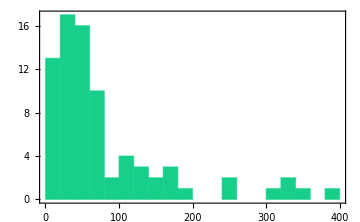
```mathematica
histogNpart[l_List]:=Module[{n,temp},temp=StringSplit[#,"\n"][[1]]&/@Rest[l];
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n={#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&/@temp;

Labeled[Histogram[(ToExpression[ToString[#]])&/@n[[All,1]],25,ImageSize->Medium,myTickStyle,ChartStyle->mycolor,Frame->True,FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->fontSize]],myStyle["Histogram for n participants \n("~~ToString[Length@n] ~~" studies included from "~~ ToString[Length@l]~~")"]]]

histogNpart[d[[All,4]]]
-Graphics-"Histogram for n participants \n(78 studies included from 80)"
histogNpart[#]&/@groups[[All,All,4]];
Labeled[#[[1]],#[[2]]]&/@Transpose[{%,myStyleFunction[{"Classical Music","Rock/Pop/Jazz","Traditional Music","Military Music"}]}]
```

## Histogram Normal Hearing

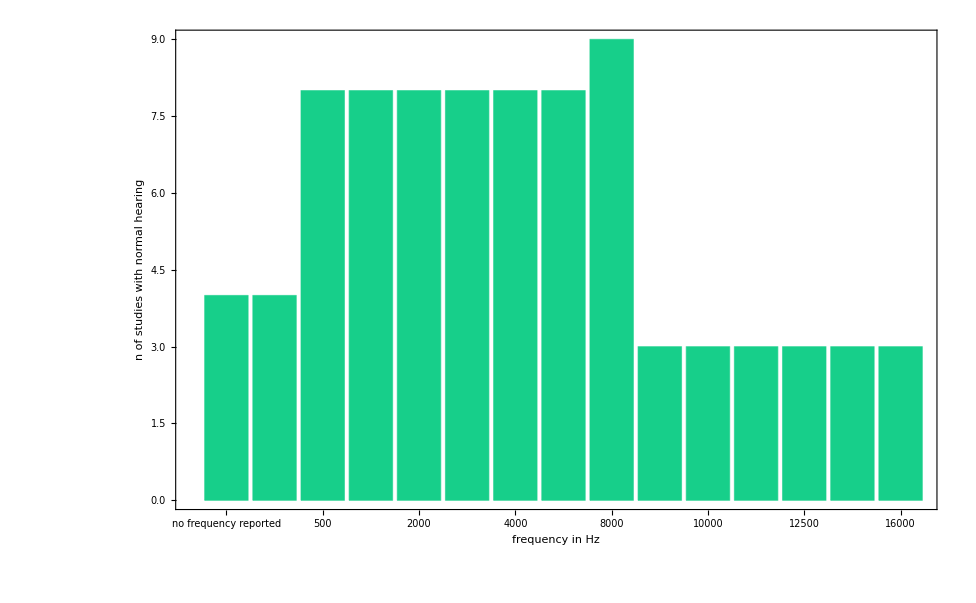
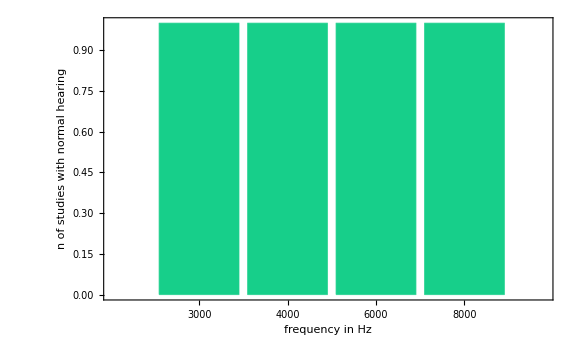
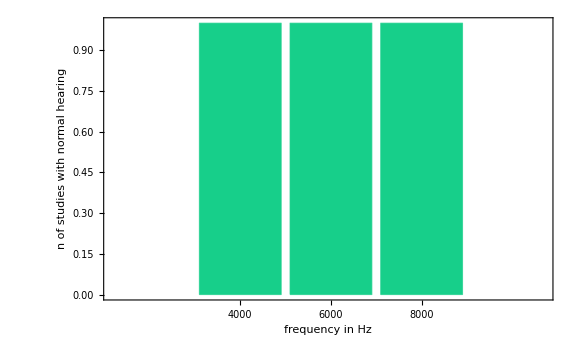
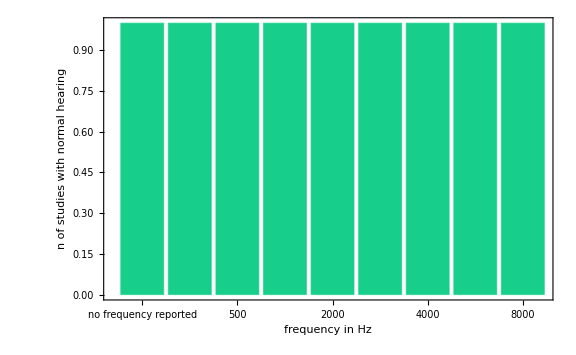
{-Graphics-Classical Music,-Graphics-Rock, Pop, Jazz,-Graphics-Traditional Music, Dance,-Graphics-Military Music, Marching Bands}

```mathematica
normalHearingHisto[l_List]:=Module[{temp,chartdata,graphNormal,normHearresultWOFR,normHearresultWIFR},
temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringJoin[#]&,StringJoin[#]]&/@#&,#,2]&/@temp;
temp=MapAt[ToExpression//@StringReplace[#,"~"->""]&,#,2]&/@(temp/."**"->{"-1"});
normHearresultWOFR=Select[temp,#[[2]]=={-1}&];
normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
temp=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;
chartdata=Tally/@{Flatten[normHearresultWOFR[[All,2]]],Flatten[ temp[[All,2]]]};
chartdata=MapAt[SortBy[#,First]&,chartdata,2];
chartdata=Transpose[Flatten[chartdata,1]/.-1->"no frequency\nreported"];
chartdata=Transpose/@chartdata;
chartdata=Association[Thread[chartdata[[1]]->chartdata[[2]]]];
graphNormal=BarChart[chartdata,ChartLabels->Automatic,ImageSize->Large,ChartStyle->mycolor,FrameLabel->myStyleFunction@{"frequency in Hz","n of studies\nwith normal hearing"},LabelStyle->Directive[fontStandard,fontSize],FrameTicksStyle->Directive[fontStandard,fontSize],AxesLabel->myStyleFunction[{"number of studies","frequency"}],Frame->True]
]
graphsnormal=normalHearingHisto/@(#[[Key["normal"]]]&/@resGroups) ;
Labeled[#[[1]],#[[2]],Top]&/@(Transpose[{graphsnormal,myStyleFunction@{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance","Military Music, Marching Bands"}}])
```

## DensityPlot

```mathematica
redColorFunction[ z_ ] :=CMYKColor[0,0.2+z*.4,0.2+z*.4,0];

stringFrDB[l_List]:=Module[{temp,plotListLossDataWOdB},temp=MapAt[StringSplit[#,"&"]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp;
temp=MapAt[StringCases[#,DigitCharacter]&/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,StringJoin[#]]&/@#&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten/@#&,#,2]&/@temp;
temp=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&/@#&,#,2]&/@temp;
temp=MapAt[StringCases[#,DigitCharacter]&,#,1]&/@temp;
temp=MapAt[Flatten,#,2]&/@temp;
plotListLossDataWOdB=Partition[Riffle[Flatten[temp[[All,2]]],-2,{2,-1,2}],2]]


resultGraphs[d_List]:=Module[{l,scalingFac,lossresultWOdB,lossresultdB,lossWOFr,lossWiFr,temp,plotListLoss,plotListLossData,labelsplotListLossData,plotListLossData4Histo,plotListLossData4HistoLabel},
l=d[[1]];
scalingFac=d[[2]];

lossresultWOdB=Select[l,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==True&];
lossresultdB=Select[l,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&];

temp=MapAt[StringSplit[#,"&"]&,#,2]&/@lossresultdB;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp; 
temp=MapAt[StringCases[#,DigitCharacter]&/@#&,#,2]&/@temp;
lossWOFr=Select[temp,#[[2]]=={{}}&];
lossWiFr=Select[temp,#[[2]]!={{}}&];
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,StringJoin[#]]&/@#&,#,2]&/@lossWiFr;
temp=MapAt[ToExpression//@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten/@#&,#,2]&/@temp;
temp=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten,#,2]&/@temp;
temp= MapAt[StringCases[#,DigitCharacter]&,#,1]&/@temp;
plotListLoss=MapAt[(ToExpression[StringJoin[#]])&,#,1]&/@temp;

plotListLossData=Transpose/@({#[[1]],Table[#[[2]],Length@#[[1]]]}&/@plotListLoss[[All,{2,1}]]);
labelsplotListLossData=Transpose[{Table[i,{i,1,Length@plotListLoss[[All,-1]]}],plotListLoss[[All,-1]]}];
plotListLossData4Histo=Transpose[{plotListLossData,labelsplotListLossData[[All,1]]}];
plotListLossData4Histo={#[[1]],Table[#[[-1]],Length@#[[1]]]}&/@plotListLossData4Histo;
plotListLossData4Histo=Transpose/@plotListLossData4Histo;
plotListLossData4HistoLabel=Labeled[#[[1]],#[[2]],Right]&/@Flatten[plotListLossData4Histo,1];
lossWOFr=ToExpression/@(StringJoin/@(StringCases[#,DigitCharacter]&/@lossWOFr[[All,1]]));
lossWOFr=Transpose[{Table[-100,Length@lossWOFr],lossWOFr}];
{ListPlot[plotListLossData4HistoLabel,ImageSize->Large,PlotRange->{{100, 8100},Automatic},ScalingFunctions->{"Log","Reverse"},Ticks->{audiometryFrList,Automatic},TicksStyle->Directive[FontFamily->fontStandard,FontSize->fontSize]],
densHisto=DensityHistogram[Join[Flatten[plotListLossData,1],lossWOFr,stringFrDB[lossresultWOdB]],scalingFac,ImageSize->Large,PlotRange->{{-100,9000},{1.5,-35}},FrameLabel->myStyleFunction@{"frequency in Hz","loss in dB"},FrameTicks->{{All,Automatic},{Delete[audiometryFrList[[1;;9]],2],Delete[audiometryFrList[[1;;9]],2]}},ScalingFunctions->{Automatic,"Reverse"},FrameTicksStyle->Directive[fontStandard,fontSize],ColorFunction->redColorFunction,ChartLegends->Automatic,ChartElementFunction->"Bubble",GridLines->{Prepend[{#,Thin}&/@audiometryFrList[[1;;9]],{-300,Directive[Gray,Thickness[.06]]}],{{-1.8,,Directive[Gray,Thickness[.09]]}}}],
Histogram[{Flatten[plotListLossData,1][[All,1]],stringFrDB[lossresultWOdB][[All,1]]},10,ChartLayout->"Stacked",ImageSize->Large,ChartStyle->colors,TicksStyle->Directive[FontFamily->fontStandard,FontSize->fontSize]]}]

graphList=resultGraphs/@{{resultGroupsLoss,37},{resultGroupsNotch,38}}

results[l_List]:=Module[{res,resultGroups,resultGroupsNormal,resultGroupsLoss,resultGroupsNotch,temp,normHearresultWOFR,normHearresultWIFR,chartdata,graphNormalHearing,graphList},
res={#[[1]],StringSplit[#[[2]],"__"]}&/@({#[[1]],StringSplit[#[[2]],",__"]}&/@Rest[l]);
resultGroups=Map[nameresult[#]&,res]/."worse hearing"->"notch";

resultGroups=Map[Which[StringContainsQ[#[[1]],"normal"],"normal"->#,StringContainsQ[#[[1]],"loss"],"loss"->#,StringContainsQ[#[[1]],"notch"],"notch"->#]&,Flatten[resultGroups,1]];
resultGroups=GroupBy[resultGroups,Keys];


resultGroupsNormal=resultGroups[[1,All,2]];
resultGroupsLoss=resultGroups[[2,All,2]];
resultGroupsNotch=resultGroups[[3,All,2]];

temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@resultGroupsNormal;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringJoin[#]&,StringJoin[#]]&/@#&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@(temp/. "**"->{"-1"});
normHearresultWOFR=Select[temp,#[[2]]=={-1}&];
normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
temp=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;
chartdata=Tally/@{Flatten[normHearresultWOFR[[All,2]]],Flatten[temp[[All,2]]]};
chartdata= SortBy[Flatten[chartdata,1],#[[1]]&];
chartdata=Transpose[chartdata/. -1->"no frequency\nreported"];
graphNormalHearing=BarChart[chartdata[[2]],ChartLabels->chartdata[[1]],ChartStyle->mycolor,ImageSize->Large,LabelStyle->Directive[fontStandard,fontSize],FrameTicksStyle->Directive[fontStandard,fontSize],AxesLabel->myStyleFunction[{"number of studies","frequency"}],Frame->True];
{graphNormalHearing,graphList};
graphList=resultGraphs/@{{resultGroupsLoss,37},{resultGroupsNotch,38}}

]
(results[#[[All,{1,10}]]]&/@{nClassic,nRPJ,nTrad,nMil})[[All,All,{2,3}]]
```

Keys::invrl: The argument Null is not a valid Association or a list of rules.

## Age Analysis

```mathematica
ageAnalysis[l_List]:=Module[{agerange,agerangesorted,intervallist},agerange=StringSplit[#,"\n"]&/@Rest[l];
agerange=StringSplit[#,{"-","–"}]&/@Select[First/@agerange,#!="-"&&#!="?"&];
agerange=ToExpression/@agerange;
agerange=({#[[2]]-#[[1]],#[[1]],#[[2]]}&/@agerange/.Null->10);
agerangesorted=SortBy[agerange,First][[All,2;;3]];
intervallist=Interval[{#[[1]],#[[2]]}]&/@agerangesorted;
{Labeled[NumberLinePlot[intervallist,{x,10,80},Frame->True,ImageSize->Large,PlotStyle->Reverse@colors,TicksStyle->Directive[FontFamily->fontStandard]],myStyle["Age Range\n("~~ToString[Length@agerange] ~~" studies included from "~~ ToString[Length@l]~~")"]],Labeled[Histogram[agerangesorted[[All,2]],10,ChartStyle->mycolor,ImageSize->Large,myTickStyle],myStyle["Histogram upper age bound\n("~~ToString[Length@agerange] ~~" studies included from "~~ ToString[Length@l]~~")"]]}]


ageAnalysis[d[[All,5]]]
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

{-Graphics-Age Range
(57 studies included from 80),-Graphics-Histogram upper age bound
(57 studies included from 80)}

```mathematica
ageAnalysis[#]&/@groups[[All,All,5]];
Column[Labeled[#[[1]],#[[2]]]&/@Transpose[{%,myStyleFunction[{"Classical Music","Rock/Pop/Jazz","Traditional Music","Military Music"}]}]];
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

Module::lvset: Local variable specification {Set[«2»],Set[«2»],Set[«2»],Set[«2»]} contains Set[«2»], which is an assignment to «2»; only assignments to symbols are allowed.

DynamicModule::lvsym: Local variable specification {Set[«2»],Set[«2»],Set[«2»],Set[«2»]} contains Set[«2»], which is not a symbol or an assignment to a symbol.

General::stop: Further output of DynamicModule::lvsym will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Module::lvset: Local variable specification {Set[«2»],Set[«2»],Set[«2»],Set[«2»]} contains Set[«2»], which is an assignment to «2»; only assignments to symbols are allowed.

General::stop: Further output of Module::lvset will be suppressed during this calculation.